```mathematica
Needs["Benchmarking`"];
BenchmarkReport[]
```

NotebookObject[ | MathematicaMark8 Report]

```mathematica
136/2
```

```mathematica
∑_(i=1)^7 i^2
```

140

```mathematica
N[√68]
```

8.24621

```mathematica
x
```

x

```mathematica
x:=11212
y:=2^80-1
Partition[Join[Table[0,{i,1,a^2-Length[IntegerDigits[x,2]]}],IntegerDigits[x,2]],10]//MatrixForm
136>Total[IntegerDigits[x,2]]
Partition[Join[Table[0,{a,1,100-Length[IntegerDigits[y,2]]}],IntegerDigits[y,2]],10]//MatrixForm
136>Total[IntegerDigits[x,2]]+Total[IntegerDigits[y,2]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0)

True

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

True

```mathematica
x:=2
a:=4
Partition[Join[Table[0,{i,1,a^2-Length[IntegerDigits[x,2]]}],IntegerDigits[x,2]],a]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

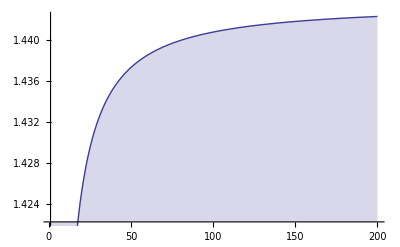

```mathematica
Monitor[DiscretePlot[∑_(x=1)^aa (∑_(i=1)^x ∑_(j=1)^x GCD[i,j])^-1,{aa,1,200}],{aa,i,j}]
```

```mathematica
Monitor[∑_(x=1)^1000 (∑_(i=1)^x ∑_(j=1)^x GCD[i,j])^-1,{x,i,j}]
```

```mathematica
N[170594658724151895853931471957834579757418579172344811702167478306983660542448193900840042367389091890487571241307835906927444268276667467171150841359511685590722514214596535266081565629504156624268006067165330125610072202490911102196613044323085158190261336410993206689067722237494868618833406626565964560381071764693518865788583734345215708285312262188644943523046332465270337530731264972067428027042671949498291675566070810493627707570400448945365296500565503082596870518164217626053131040605958243135926095614652025438661765294931426833790769782369519114594807097796840601549975115666321618820261644291098156692457766134501724970570259104354342577896125418768602060267439405353261861928313829118470022030837757225149924510371970600583360579788873605953265960386507543157152597970122362368037641992058281937353963470082964913832956540660515830961856634797691904220579039733564858969017212515749014333250924321002423252356547081282808418345950842063624342045125723406338123843752229009982250842299259861132824556405747387702337609236430407091566297595259439630764551770768108873115222372518891977449621044235424754953778733475808916573518166511077554608292724560503299972620014409705416327608029100553084738452006714975147076428042535813770236870382052242059667590789279141321636428347141188470420856112849930323955893643975216737171241819127186098598072913364826223395399763124370095721718811623383801826506331678105115172561584461256970698751897384409588322527802354108636340615108936980551571768417253485108189584889676197577221572211492297077016285544756491560179206369188690080355119861123955132626242380815275223237766023505209924174962392137898322569970498231331654132718430000870542910861205518388807250286488487281003521767577764446563501285467967054463474489457909429298615557199734846547735896195564492341625477599576153995829190295954339289819693226780699098458831332573094422472996626084663067616312861072788155125470216121848912908042123412120479102154937465271745916853771565406718449886160092861474297989287002382618768572135489463622151818078366592272834135257729503788325369167381293182257708282906996989096096637990855294238794177384789252610115861979177802597520125534973506225560584962647807977919664745868292445612897581368386403808307101182080449190144553347718906608330144622879459189917356151980077796625968321371796057815832641372998413619195069768982993182839980775035156758994214935707000228135730092362922184218776958653179405621633545217036119592803326117341659579232917371915372807599236811955044137109397047462906895331681731417266008145680456530135815230289744111808164927618676660753389855742018782510582294751310132599535188461833557096623805256080286248359448064249635118663779051223921558445557755672731400184381096552756975989963987727914585825209374771268669373174060745396150505646005375222174398970315075955355690530211561824243198305751774544661353199558858646311581053296849466390746033636461677753886006981615089354836357251691357/118192069843753786854150794118366374075500257748980540877202105759849496860949898233790390984182099116356240616484652448509593227566701189826287419665053946827870280932236912552261865340726525665980304805165302799818792916601882852253391197820022716922159158507501099054235079393038742420379167845128058714705364821962044265391310582196073255206266210184165522776319164933702835885040414549257194285961241769317184806581716491898946998218222392070024536638546005930312927252989174861680353684459708239332379778726321524820747890555479096359950288898010765284773483518076321971147293580421306678695957653839913929151826130719204693455563980642545720990160453726414946739725943017190503238362264431615648600938266625649527714828895960690897658356108203410336052993323124150186576855316782281396029043889991746504948401174429575512038248473345252780968251172895115610888981147591394240076713952373857286303166959075889180454936314675979836397368175707322094081068759227766795284453730839523875957022250809708603603977416795069368271877524926051347106498435821502113488691745371838879243585890588451659112331386002140563225562878036255766959445795169101577098935275820891142882581573512733752338011207153682461757365284553419521938277551146414492710337708145565525873702423572262991693982835617208098749823467176203729451234301454254567839007964709670752510219633090929558885656525594615596912208089898902709723518752195497045836521712124138562976974861892537878790339857203590137742049445152307191647592478919193383692181602533538504684660479284095164221766545218022816233548120267292683416924469331514552497382972319536200224933658328632388870926439725823399489728247085840802158300600109145357780257574519368019015504866348819776774123525118955959241723161319629961391217359220430594435604882457220793356896170393128242936535941300615275267477074290782315626100471338768794172791438826513384117468379340450383531053066718076513950266210556190742816068336492803905513038304439957433698200231305092768086397572349915171516743071920681050662319951884542588625193886367433942699192815457956562249961455545471096438736109125065116095871560135966713471961558698545027102507980797367962843986893863532663617281265860335823734709692398448223202336777245970872242261436962448633735982426942436447116303906899193727748551609879940230989834291232993425605375256747831249543183788074721546411249063131695154120406689639186032633381124653320498983097868019280169963328266815607650758318555294620687084399451713379684215526469780039377437194203169643030499786232669519165726996235767134811948987874541883101530218906859686018562791682880198711113343553688472121734600548162272153043785808628382881134688682940519010057182494828903586990011384655086985785295812257742926656552534629563754760737798858386137824145515604280202217577736595884020529739822289992489773326123716690422556823110841230748551023421047728567360850095032010444748232762572393829265579071940580383629774166685843967360000,100]
```

1.443368061407780484972999516984573868682318234261830835179975800429308439143886716316231351147289672

```mathematica
FactorInteger[Numerator[170594658724151895853931471957834579757418579172344811702167478306983660542448193900840042367389091890487571241307835906927444268276667467171150841359511685590722514214596535266081565629504156624268006067165330125610072202490911102196613044323085158190261336410993206689067722237494868618833406626565964560381071764693518865788583734345215708285312262188644943523046332465270337530731264972067428027042671949498291675566070810493627707570400448945365296500565503082596870518164217626053131040605958243135926095614652025438661765294931426833790769782369519114594807097796840601549975115666321618820261644291098156692457766134501724970570259104354342577896125418768602060267439405353261861928313829118470022030837757225149924510371970600583360579788873605953265960386507543157152597970122362368037641992058281937353963470082964913832956540660515830961856634797691904220579039733564858969017212515749014333250924321002423252356547081282808418345950842063624342045125723406338123843752229009982250842299259861132824556405747387702337609236430407091566297595259439630764551770768108873115222372518891977449621044235424754953778733475808916573518166511077554608292724560503299972620014409705416327608029100553084738452006714975147076428042535813770236870382052242059667590789279141321636428347141188470420856112849930323955893643975216737171241819127186098598072913364826223395399763124370095721718811623383801826506331678105115172561584461256970698751897384409588322527802354108636340615108936980551571768417253485108189584889676197577221572211492297077016285544756491560179206369188690080355119861123955132626242380815275223237766023505209924174962392137898322569970498231331654132718430000870542910861205518388807250286488487281003521767577764446563501285467967054463474489457909429298615557199734846547735896195564492341625477599576153995829190295954339289819693226780699098458831332573094422472996626084663067616312861072788155125470216121848912908042123412120479102154937465271745916853771565406718449886160092861474297989287002382618768572135489463622151818078366592272834135257729503788325369167381293182257708282906996989096096637990855294238794177384789252610115861979177802597520125534973506225560584962647807977919664745868292445612897581368386403808307101182080449190144553347718906608330144622879459189917356151980077796625968321371796057815832641372998413619195069768982993182839980775035156758994214935707000228135730092362922184218776958653179405621633545217036119592803326117341659579232917371915372807599236811955044137109397047462906895331681731417266008145680456530135815230289744111808164927618676660753389855742018782510582294751310132599535188461833557096623805256080286248359448064249635118663779051223921558445557755672731400184381096552756975989963987727914585825209374771268669373174060745396150505646005375222174398970315075955355690530211561824243198305751774544661353199558858646311581053296849466390746033636461677753886006981615089354836357251691357/118192069843753786854150794118366374075500257748980540877202105759849496860949898233790390984182099116356240616484652448509593227566701189826287419665053946827870280932236912552261865340726525665980304805165302799818792916601882852253391197820022716922159158507501099054235079393038742420379167845128058714705364821962044265391310582196073255206266210184165522776319164933702835885040414549257194285961241769317184806581716491898946998218222392070024536638546005930312927252989174861680353684459708239332379778726321524820747890555479096359950288898010765284773483518076321971147293580421306678695957653839913929151826130719204693455563980642545720990160453726414946739725943017190503238362264431615648600938266625649527714828895960690897658356108203410336052993323124150186576855316782281396029043889991746504948401174429575512038248473345252780968251172895115610888981147591394240076713952373857286303166959075889180454936314675979836397368175707322094081068759227766795284453730839523875957022250809708603603977416795069368271877524926051347106498435821502113488691745371838879243585890588451659112331386002140563225562878036255766959445795169101577098935275820891142882581573512733752338011207153682461757365284553419521938277551146414492710337708145565525873702423572262991693982835617208098749823467176203729451234301454254567839007964709670752510219633090929558885656525594615596912208089898902709723518752195497045836521712124138562976974861892537878790339857203590137742049445152307191647592478919193383692181602533538504684660479284095164221766545218022816233548120267292683416924469331514552497382972319536200224933658328632388870926439725823399489728247085840802158300600109145357780257574519368019015504866348819776774123525118955959241723161319629961391217359220430594435604882457220793356896170393128242936535941300615275267477074290782315626100471338768794172791438826513384117468379340450383531053066718076513950266210556190742816068336492803905513038304439957433698200231305092768086397572349915171516743071920681050662319951884542588625193886367433942699192815457956562249961455545471096438736109125065116095871560135966713471961558698545027102507980797367962843986893863532663617281265860335823734709692398448223202336777245970872242261436962448633735982426942436447116303906899193727748551609879940230989834291232993425605375256747831249543183788074721546411249063131695154120406689639186032633381124653320498983097868019280169963328266815607650758318555294620687084399451713379684215526469780039377437194203169643030499786232669519165726996235767134811948987874541883101530218906859686018562791682880198711113343553688472121734600548162272153043785808628382881134688682940519010057182494828903586990011384655086985785295812257742926656552534629563754760737798858386137824145515604280202217577736595884020529739822289992489773326123716690422556823110841230748551023421047728567360850095032010444748232762572393829265579071940580383629774166685843967360000]]
```

{{2,10},{3,7},{5,4},{7,3},{11,3},{13,2},{17,1},{19,2},{23,2},{29,1},{31,2},{37,1},{41,2},{43,1},{47,2},{53,1},{59,1},{61,1},{67,1},{71,1},{73,1},{79,1},{83,1},{89,1},{97,1},{101,1},{103,1},{107,1},{109,1},{113,2},{127,1},{131,1},{137,1},{139,1},{149,1},{151,1},{157,1},{163,1},{167,1},{173,1},{179,1},{181,1},{191,1},{193,1},{197,1},{199,1},{211,1},{223,1},{227,1},{229,1},{233,1},{239,1},{241,1},{251,1},{257,1},{269,1},{271,1},{277,1},{281,1},{283,1},{293,1},{307,1},{311,1},{313,1},{317,1},{331,1},{337,1},{347,1},{349,1},{353,1},{359,1},{367,1},{373,1},{383,1},{389,1},{397,1},{401,1},{409,1},{419,1},{421,1},{431,1},{433,1},{439,1},{443,1},{449,1},{457,1},{461,1},{463,1},{467,1},{479,1},{487,1},{491,1},{499,1},{503,1},{509,1},{523,1},{541,1},{547,1},{557,1},{563,1},{569,1},{571,1},{587,1},{593,1},{599,1},{601,1},{607,1},{613,1},{617,1},{619,1},{631,1},{647,1},{653,1},{659,1},{661,1},{677,1},{683,1},{691,1},{701,1},{709,1},{727,1},{733,1},{739,1},{743,1},{757,1},{761,1},{773,1},{787,1},{797,1},{809,1},{821,1},{827,1},{829,1},{853,1},{863,1},{877,1},{887,1},{907,1},{919,1},{929,1},{937,1},{947,1},{953,1},{967,1},{971,1},{997,1},{1009,1},{1021,1},{1033,1},{1039,1},{1051,1},{1063,1},{1069,1},{1087,1},{1091,1},{1093,1},{1109,1},{1151,1},{1153,1},{1163,1},{1187,1},{1193,1},{1201,1},{1229,1},{1277,1},{1279,1},{1283,1},{1291,1},{1297,1},{1301,1},{1307,1},{1321,1},{1361,1},{1373,1},{1381,1},{1399,1},{1409,1},{1427,1},{1439,1},{1447,1},{1451,1},{1459,1},{1471,1},{1493,1},{1543,1},{1553,1},{1571,1},{1583,1},{1609,1},{1637,1},{1697,1},{1709,1},{1783,1},{1787,1},{1789,1},{1801,1},{1823,1},{1831,1},{1867,1},{1871,1},{1877,1},{1907,1},{1913,1},{1979,1},{1993,1},{1997,1},{2017,1},{2039,1},{2089,1},{2099,1},{2129,1},{2141,1},{2143,1},{2239,1},{2243,1},{2251,1},{2273,1},{2281,1},{2333,1},{2341,1},{2357,1},{2377,1},{2381,1},{2383,1},{2393,1},{2399,1},{2417,1},{2423,1},{2437,1},{2441,1},{2447,1},{2459,1},{2467,1},{2473,1},{2503,1},{2521,1},{2531,1},{2551,1},{2557,1},{2591,1},{2617,1},{2647,1},{2683,1},{2699,1},{2707,1},{2713,1},{2753,1},{2791,1},{2797,1},{2833,1},{2851,1},{2939,1},{2963,1},{3023,1},{3037,1},{3049,1},{3061,1},{3109,1},{3137,1},{3181,1},{3229,1},{3301,1},{3319,1},{3359,1},{3373,1},{3389,1},{3391,1},{3413,1},{3433,1},{3461,1},{3539,1},{3541,1},{3571,1},{3593,1},{3623,1},{3631,1},{3697,1},{3701,1},{3733,1},{3767,1},{3769,1},{3779,1},{3823,1},{3853,1},{3877,1},{3929,1},{3967,1},{4001,1},{4027,1},{4079,1},{4091,1},{4231,1},{4273,1},{4327,1},{4349,1},{4397,1},{4447,1},{4451,1},{4481,1},{4483,1},{4493,1},{4519,1},{4523,1},{4583,1},{4603,1},{4621,1},{4649,1},{4673,1},{4679,1},{4691,1},{4721,1},{4783,1},{4789,1},{4799,1},{4813,1},{4817,1},{4909,1},{4951,1},{5021,1},{5051,1},{5107,1},{5171,1},{5179,1},{5189,1},{5209,1},{5261,1},{5393,1},{5483,1},{5503,1},{5521,1},{5711,1},{5791,1},{5807,1},{5821,1},{5827,1},{6079,1},{6271,1},{6317,1},{6389,1},{6449,1},{6469,1},{6491,1},{6551,1},{6563,1},{6661,1},{6761,1},{6763,1},{6883,1},{7019,1},{7177,1},{7213,1},{7489,1},{7499,1},{7561,1},{8053,1},{8179,1},{8353,1},{8537,1},{8543,1},{8563,1},{8627,1},{8641,1},{8669,1},{8713,1},{8893,1},{9041,1},{9049,1},{9137,1},{9323,1},{9533,1},{9587,1},{9629,1},{9839,1},{9859,1},{10259,1},{10343,1},{10459,1},{10657,1},{10691,1},{10789,1},{10847,1},{10939,1},{10993,1},{11279,1},{11299,1},{11329,1},{11497,1},{12071,1},{12149,1},{12281,1},{12451,1},{12511,1},{12917,1},{13099,1},{13679,1},{14033,1},{14197,1},{14387,1},{14407,1},{14419,1},{14437,1},{14489,1},{14879,1},{14947,1},{14969,1},{15091,1},{15473,1},{15647,1},{16417,1},{16657,1},{16759,1},{16937,1},{17047,1},{17317,1},{17539,1},{17581,1},{17989,1},{18169,1},{18401,1},{18671,1},{19207,1},{19379,1},{19541,1},{19819,1},{19973,1},{20047,1},{20323,1},{20353,1},{20357,1},{20759,1},{21101,1},{21139,1},{21169,1},{21803,1},{22093,1},{22571,1},{22811,1},{22853,1},{23561,1},{23719,1},{23857,1},{23873,1},{24113,1},{24499,1},{24809,1},{24923,1},{24989,1},{25057,1},{25841,1},{25849,1},{25981,1},{26111,1},{26309,1},{26539,1},{26881,1},{27143,1},{27479,1},{27509,1},{27581,1},{27737,1},{27817,1},{28657,1},{30631,1},{30859,1},{30983,1},{31729,1},{32297,1},{32299,1},{32531,1},{32971,1},{33529,1},{33623,1},{33751,1},{34061,1},{34537,1},{35051,1},{35671,1},{35747,1},{36007,1},{36373,1},{36473,1},{36637,1},{36913,1},{36973,1},{37019,1},{37087,1},{38011,1},{38153,1},{38371,1},{38449,1},{39107,1},{39733,1},{40009,1},{40361,1},{40493,1},{41051,1},{41131,1},{42197,1},{42209,1},{42533,1},{42967,1},{43609,1},{43787,1},{44771,1},{45817,1},{46993,1},{47419,1},{47639,1},{48337,1},{49369,1},{50231,1},{50387,1},{51151,1},{51941,1},{52673,1},{55259,1},{55411,1},{56263,1},{56909,1},{57149,1},{57709,1},{57859,1},{58439,1},{58913,1},{58967,1},{59863,1},{60607,1},{61781,1},{64763,1},{65063,1},{65213,1},{65717,1},{67733,1},{67843,1},{68261,1},{68477,1},{69493,1},{70459,1},{71563,1},{72823,1},{72937,1},{72949,1},{73597,1},{74489,1},{74561,1},{75289,1},{76079,1},{76123,1},{76231,1},{77761,1},{78577,1},{81281,1},{82891,1},{83617,1},{84913,1},{85061,1},{85303,1},{86117,1},{86399,1},{87041,1},{88661,1},{89303,1},{89563,1},{90011,1},{90911,1},{91009,1},{94063,1},{94613,1},{94709,1},{95021,1},{95189,1},{95629,1},{96553,1},{97847,1},{99923,1},{106163,1},{106721,1},{107137,1},{107347,1},{108761,1},{109471,1},{114407,1},{115777,1},{116959,1},{118583,1},{121591,1},{122231,1},{123517,1},{126223,1},{132619,1},{133733,1},{134807,1},{135757,1},{136207,1},{136261,1},{138373,1},{138629,1},{140977,1},{143807,1},{149503,1},{152441,1},{156493,1},{157457,1},{158209,1},{165203,1},{166561,1},{169181,1},{171043,1},{172801,1},{177533,1},{178223,1},{179623,1},{186157,1},{186917,1},{193601,1},{199417,1},{199831,1},{200903,1},{201623,1},{202921,1},{206489,1},{216649,1},{219523,1},{219847,1},{225383,1},{225509,1},{225527,1},{227219,1},{239521,1},{243953,1},{244009,1},{255197,1},{256577,1},{266029,1},{267469,1},{267893,1},{268043,1},{276781,1},{281551,1},{284051,1},{288907,1},{290393,1},{294391,1},{296683,1},{312241,1},{322097,1},{324427,1},{330877,1},{334049,1},{334493,1},{337367,1},{367189,1},{376003,1},{379277,1},{387449,1},{397433,1},{400109,1},{402541,1},{407741,1},{421273,1},{423431,1},{442283,1},{476713,1},{500249,1},{502081,1},{527063,1},{527699,1},{543097,1},{574183,1},{575689,1},{577613,1},{581947,1},{623341,1},{629143,1},{654529,1},{660167,1},{710119,1},{729271,1},{739183,1},{740279,1},{763559,1},{775949,1},{785413,1},{803237,1},{863801,1},{914237,1},{946031,1},{958577,1},{1052573,1},{1066433,1},{1106653,1},{1191439,1},{1229773,1},{1267381,1},{1274509,1},{1310093,1},{1425503,1},{1433587,1},{1438501,1},{1628401,1},{1740197,1},{1764313,1},{1773413,1},{1911109,1},{2003081,1},{2032213,1},{2233373,1},{2287013,1},{2353517,1},{2371801,1},{2408837,1},{2423521,1},{2514229,1},{2711521,1},{2890081,1},{2927669,1},{2985973,1},{3081413,1},{3144829,1},{3365213,1},{3430573,1},{3531989,1},{3565013,1},{3606277,1},{3639509,1},{3945841,1},{3989837,1},{4014281,1},{4050149,1},{4054933,1},{4118501,1},{4418069,1}}

```mathematica
FactorInteger[Numerator[170594658724151895853931471957834579757418579172344811702167478306983660542448193900840042367389091890487571241307835906927444268276667467171150841359511685590722514214596535266081565629504156624268006067165330125610072202490911102196613044323085158190261336410993206689067722237494868618833406626565964560381071764693518865788583734345215708285312262188644943523046332465270337530731264972067428027042671949498291675566070810493627707570400448945365296500565503082596870518164217626053131040605958243135926095614652025438661765294931426833790769782369519114594807097796840601549975115666321618820261644291098156692457766134501724970570259104354342577896125418768602060267439405353261861928313829118470022030837757225149924510371970600583360579788873605953265960386507543157152597970122362368037641992058281937353963470082964913832956540660515830961856634797691904220579039733564858969017212515749014333250924321002423252356547081282808418345950842063624342045125723406338123843752229009982250842299259861132824556405747387702337609236430407091566297595259439630764551770768108873115222372518891977449621044235424754953778733475808916573518166511077554608292724560503299972620014409705416327608029100553084738452006714975147076428042535813770236870382052242059667590789279141321636428347141188470420856112849930323955893643975216737171241819127186098598072913364826223395399763124370095721718811623383801826506331678105115172561584461256970698751897384409588322527802354108636340615108936980551571768417253485108189584889676197577221572211492297077016285544756491560179206369188690080355119861123955132626242380815275223237766023505209924174962392137898322569970498231331654132718430000870542910861205518388807250286488487281003521767577764446563501285467967054463474489457909429298615557199734846547735896195564492341625477599576153995829190295954339289819693226780699098458831332573094422472996626084663067616312861072788155125470216121848912908042123412120479102154937465271745916853771565406718449886160092861474297989287002382618768572135489463622151818078366592272834135257729503788325369167381293182257708282906996989096096637990855294238794177384789252610115861979177802597520125534973506225560584962647807977919664745868292445612897581368386403808307101182080449190144553347718906608330144622879459189917356151980077796625968321371796057815832641372998413619195069768982993182839980775035156758994214935707000228135730092362922184218776958653179405621633545217036119592803326117341659579232917371915372807599236811955044137109397047462906895331681731417266008145680456530135815230289744111808164927618676660753389855742018782510582294751310132599535188461833557096623805256080286248359448064249635118663779051223921558445557755672731400184381096552756975989963987727914585825209374771268669373174060745396150505646005375222174398970315075955355690530211561824243198305751774544661353199558858646311581053296849466390746033636461677753886006981615089354836357251691357/118192069843753786854150794118366374075500257748980540877202105759849496860949898233790390984182099116356240616484652448509593227566701189826287419665053946827870280932236912552261865340726525665980304805165302799818792916601882852253391197820022716922159158507501099054235079393038742420379167845128058714705364821962044265391310582196073255206266210184165522776319164933702835885040414549257194285961241769317184806581716491898946998218222392070024536638546005930312927252989174861680353684459708239332379778726321524820747890555479096359950288898010765284773483518076321971147293580421306678695957653839913929151826130719204693455563980642545720990160453726414946739725943017190503238362264431615648600938266625649527714828895960690897658356108203410336052993323124150186576855316782281396029043889991746504948401174429575512038248473345252780968251172895115610888981147591394240076713952373857286303166959075889180454936314675979836397368175707322094081068759227766795284453730839523875957022250809708603603977416795069368271877524926051347106498435821502113488691745371838879243585890588451659112331386002140563225562878036255766959445795169101577098935275820891142882581573512733752338011207153682461757365284553419521938277551146414492710337708145565525873702423572262991693982835617208098749823467176203729451234301454254567839007964709670752510219633090929558885656525594615596912208089898902709723518752195497045836521712124138562976974861892537878790339857203590137742049445152307191647592478919193383692181602533538504684660479284095164221766545218022816233548120267292683416924469331514552497382972319536200224933658328632388870926439725823399489728247085840802158300600109145357780257574519368019015504866348819776774123525118955959241723161319629961391217359220430594435604882457220793356896170393128242936535941300615275267477074290782315626100471338768794172791438826513384117468379340450383531053066718076513950266210556190742816068336492803905513038304439957433698200231305092768086397572349915171516743071920681050662319951884542588625193886367433942699192815457956562249961455545471096438736109125065116095871560135966713471961558698545027102507980797367962843986893863532663617281265860335823734709692398448223202336777245970872242261436962448633735982426942436447116303906899193727748551609879940230989834291232993425605375256747831249543183788074721546411249063131695154120406689639186032633381124653320498983097868019280169963328266815607650758318555294620687084399451713379684215526469780039377437194203169643030499786232669519165726996235767134811948987874541883101530218906859686018562791682880198711113343553688472121734600548162272153043785808628382881134688682940519010057182494828903586990011384655086985785295812257742926656552534629563754760737798858386137824145515604280202217577736595884020529739822289992489773326123716690422556823110841230748551023421047728567360850095032010444748232762572393829265579071940580383629774166685843967360000]]
```

$Aborted

```mathematica
Monitor[Table[(∑_(i=1)^x ∑_(j=1)^x GCD[i,j]),{x,1,1000}],{x,i,j}]
```

```mathematica
1/{1,5,12,24,37,61,80,112,145,189,220,288,325,389,464,544,593,701,756,880,989,1093,1160,1336,1441,1565,1700,1880,1965,2205,2296,2488,2665,2829,3028,3328,3437,3621,3832,4152,4273,4621,4748,5040,5373,5597,5736,6168,6385,6725,7004,7352,7509,7941,8264,8728,9041,9325,9500,10160,10341,10645,11128,11576,11961,12525,12724,13184,13565,14197,14408,15176,15393,15757,16332,16848,17317,17989,18224,19008,19521,19925,20172,21128,21637,22061,22544,23296,23561,24605,25164,25792,26309,26773,27344,28368,28657,29357,30140,31080,31381,32269,32576,33472,34537,35061,35380,36568,36893,37917,38536,39672,40009,41005,41700,42496,43429,44013,44752,46432,46993,47597,48284,49136,49861,51373,51752,52776,53497,54717,55108,56656,57485,58149,59472,60656,61065,62277,62692,64424,65213,65917,66824,68696,69577,70301,71484,72504,72949,74749,75200,76528,77761,79245,80188,82032,82501,83285,84176,86032,87041,88661,89148,90280,92005,92829,93328,95760,96553,98165,99548,100736,101253,102789,104304,106144,107137,108021,108556,111400,111941,113709,114736,116352,117481,119125,120324,121624,123541,125349,125920,128288,128865,129829,131884,133816,134405,136853,137448,139848,140977,141981,143260,145696,146949,147973,149656,151848,153193,156493,157124,158592,159789,160853,162168,165192,166561,167645,168876,171680,173109,175077,175744,178432,180937,182061,182740,185472,186157,188357,190856,192904,193601,196517,197956,199592,200925,203261,203976,208056,208777,210581,212444,214136,216285,218469,220072,222264,223665,225965,226716,230832,232469,233733,236448,238752,239521,241813,243452,246792,248925,250229,251016,254952,256577,259197,260700,262560,263365,267469,268280,271176,274153,275517,277972,281296,282125,283509,285792,290192,291033,293541,294388,296360,299405,302269,304088,308504,309881,312669,314308,316336,317213,320909,322720,325344,328449,329933,331884,336784,338693,340197,341904,345152,347025,350877,351796,355856,357597,360581,361512,366200,367137,368701,373300,375496,376445,379277,381352,385640,387449,390637,392756,397184,400109,401733,403576,406488,408577,413917,414908,417216,419949,421613,423672,429576,430585,433133,435044,439456,441677,445997,448104,451160,454865,456589,457628,461840,462885,467605,471304,475656,476713,479869,482052,484528,488461,490245,491320,498520,500249,502053,505100,509936,512181,515445,516544,520496,523529,527101,529460,533968,535085,538869,542744,546088,548561,554501,555636,560584,562733,564637,565784,571160,575689,577613,580796,583496,584661,591021,593600,598528,600745,602709,605140,611800,612989,614973,619384,625224,626425,630013,632660,635472,640413,644453,647112,653304,654529,658493,660812,663680,666309,671565,674120,679304,681657,685901,687156,696096,697357,699461,702944,706720,710585,714389,717108,720088,724909,729069,730360,737704,739001,743325,748020,751056,753949,757861,759176,766296,771441,775949,777276,782672,785413,787637,790160,796368,797713,805453,808404,811552,814109,816373,821768,828712,830081,832365,837252,843272,844653,852381,853768,858776,863801,866125,867524,875456,878445,882997,885656,889864,892961,897197,901532,907920,911853,914237,915672,925272,928441,930845,936212,941184,944173,950005,951464,955816,958577,965269,966740,972728,975997,981053,988496,993856,997025,1001477,1002972,1009272,1012101,1014605,1016112,1026528,1029641,1034805,1039108,1042648,1044173,1052573,1055832,1060952,1066433,1068997,1072172,1078456,1081845,1087021,1089952,1098432,1099993,1106653,1108220,1111872,1119797,1122421,1125920,1135472,1138025,1143165,1147548,1154712,1158229,1163005,1166304,1171088,1174121,1176805,1181852,1192976,1194597,1197301,1200368,1207216,1210577,1219781,1221420,1225240,1229773,1237413,1241080,1249528,1253057,1255821,1261836,1265712,1267381,1274509,1278200,1288872,1295241,1298045,1299732,1306608,1310093,1312917,1320072,1325144,1326849,1336269,1337980,1345808,1349045,1354789,1360064,1370240,1371969,1376389,1379660,1387288,1390997,1396205,1400032,1405248,1414113,1417037,1418796,1428848,1432773,1438501,1441840,1448256,1450033,1459645,1466772,1470928,1474301,1480453,1482248,1494648,1496449,1502477,1507460,1511672,1517205,1522629,1524448,1532128,1538929,1544853,1548892,1559368,1561205,1564269,1570944,1581248,1583097,1588629,1590484,1598648,1605317,1608421,1612400,1623776,1628401,1631525,1638668,1643048,1647237,1661349,1663240,1668888,1672465,1675629,1679548,1687312,1693325,1699869,1705152,1714880,1716801,1722549,1724476,1733192,1740197,1746877,1748816,1760048,1764313,1773413,1780692,1785240,1787197,1793053,1797096,1804216,1809649,1816245,1818220,1832680,1834661,1837965,1845552,1851488,1859481,1868013,1872476,1877136,1880917,1887429,1891840,1905728,1907745,1911109,1920964,1927984,1930013,1936085,1940424,1951624,1955473,1962477,1964524,1976272,1980501,1987165,1991048,1998520,2003081,2014541,2016612,2021440,2032213,2035677,2039968,2050672,2055321,2058805,2062756,2075576,2077677,2089125,2093824,2103872,2111537,2115061,2119580,2128232,2130357,2137261,2143144,2149512,2154289,2166445,2175180,2180176,2184229,2187813,2189968,2207392,2212001,2217549,2221636,2226688,2233373,2242877,2245056,2257328,2263889,2270989,2275868,2284816,2287013,2290677,2301912,2311256,2316105,2325573,2327788,2337560,2346069,2353517,2355744,2367200,2371801,2375525,2381708,2392048,2396837,2408837,2411088,2419264,2423521,2431317,2435980,2452072,2454341,2458125,2466816,2479376,2481657,2488485,2493364,2498696,2510405,2514229,2519312,2531344,2533649,2547621,2551980,2557368,2559685,2569621,2576776,2583720,2592433,2596317,2601532,2618752,2623893,2632021,2640472,2652456,2657305,2664349,2666708,2672208,2676669,2684357,2689416,2706264,2711521,2715485,2724140,2729696,2732085,2745717,2751056,2764816,2771449,2775453,2780740,2790576,2800301,2808645,2813208,2820440,2822865,2838093,2840524,2851568,2856165,2864549,2869584,2884608,2890081,2894165,2906996,2917840,2920301,2927669,2930136,2937512,2950337,2958637,2961116,2975408,2977893,2985973,2990672,3002640,3010585,3018061,3023220,3034816,3043861,3048045,3050560,3073120,3077209,3081413,3086180,3092072,3099885,3110757,3118776,3128008,3132809,3144829,3150548,3160976,3163533,3172117,3185248,3192912,3195481,3210373,3212948,3224328,3233997,3238301,3240888,3258168,3263513,3267837,3275300,3287120,3292845,3307365,3313144,3320952,3328185,3337301,3347476,3358200,3360829,3365213,3370184,3387448,3390089,3405965,3408612,3420928,3430573,3434997,3437656,3451368,3457057,3465725,3477308,3483536,3489525,3497541,3503072,3517152,3527505,3531989,3538044,3558984,3565013,3574317,3584464,3592560,3598153,3606277,3608996,3615336,3622869,3639509,3642240,3659088,3665105,3669669,3679644,3686040,3691909,3707029,3709784,3725064,3730273,3734877,3741004,3761920,3770485,3775109,3782792,3794632,3797417,3812957,3821868,3828376,3833653,3838317,3849856,3869920,3872729,3882165,3887476,3899928,3902749,3911197,3917544,3927832,3945841,3955605,3958444,3970056,3976357,3989837,3995216,4011424,4014281,4026557,4032460,4039136,4050149,4054933,4061072,4083152,4087833,4097821,4105804,4112536,4118501,4135085,4137984,4150656,4161897,4171349,4174260,4190136,4196365,4201229,4216504,4227144,4230073,4238845,4245300,4263472,4271605,4276509,4279456,4294672,4300761,4311061,4322164,4335976,4342637,4365461,4368432,4381104,4386721,4396725,4402876,4415080,4418069,4423053,4433880,4449880}
```

{1,1/5,1/12,1/24,1/37,1/61,1/80,1/112,1/145,1/189,1/220,1/288,1/325,1/389,1/464,1/544,1/593,1/701,1/756,1/880,1/989,1/1093,1/1160,1/1336,1/1441,1/1565,1/1700,1/1880,1/1965,1/2205,1/2296,1/2488,1/2665,1/2829,1/3028,1/3328,1/3437,1/3621,1/3832,1/4152,1/4273,1/4621,1/4748,1/5040,1/5373,1/5597,1/5736,1/6168,1/6385,1/6725,1/7004,1/7352,1/7509,1/7941,1/8264,1/8728,1/9041,1/9325,1/9500,1/10160,1/10341,1/10645,1/11128,1/11576,1/11961,1/12525,1/12724,1/13184,1/13565,1/14197,1/14408,1/15176,1/15393,1/15757,1/16332,1/16848,1/17317,1/17989,1/18224,1/19008,1/19521,1/19925,1/20172,1/21128,1/21637,1/22061,1/22544,1/23296,1/23561,1/24605,1/25164,1/25792,1/26309,1/26773,1/27344,1/28368,1/28657,1/29357,1/30140,1/31080,1/31381,1/32269,1/32576,1/33472,1/34537,1/35061,1/35380,1/36568,1/36893,1/37917,1/38536,1/39672,1/40009,1/41005,1/41700,1/42496,1/43429,1/44013,1/44752,1/46432,1/46993,1/47597,1/48284,1/49136,1/49861,1/51373,1/51752,1/52776,1/53497,1/54717,1/55108,1/56656,1/57485,1/58149,1/59472,1/60656,1/61065,1/62277,1/62692,1/64424,1/65213,1/65917,1/66824,1/68696,1/69577,1/70301,1/71484,1/72504,1/72949,1/74749,1/75200,1/76528,1/77761,1/79245,1/80188,1/82032,1/82501,1/83285,1/84176,1/86032,1/87041,1/88661,1/89148,1/90280,1/92005,1/92829,1/93328,1/95760,1/96553,1/98165,1/99548,1/100736,1/101253,1/102789,1/104304,1/106144,1/107137,1/108021,1/108556,1/111400,1/111941,1/113709,1/114736,1/116352,1/117481,1/119125,1/120324,1/121624,1/123541,1/125349,1/125920,1/128288,1/128865,1/129829,1/131884,1/133816,1/134405,1/136853,1/137448,1/139848,1/140977,1/141981,1/143260,1/145696,1/146949,1/147973,1/149656,1/151848,1/153193,1/156493,1/157124,1/158592,1/159789,1/160853,1/162168,1/165192,1/166561,1/167645,1/168876,1/171680,1/173109,1/175077,1/175744,1/178432,1/180937,1/182061,1/182740,1/185472,1/186157,1/188357,1/190856,1/192904,1/193601,1/196517,1/197956,1/199592,1/200925,1/203261,1/203976,1/208056,1/208777,1/210581,1/212444,1/214136,1/216285,1/218469,1/220072,1/222264,1/223665,1/225965,1/226716,1/230832,1/232469,1/233733,1/236448,1/238752,1/239521,1/241813,1/243452,1/246792,1/248925,1/250229,1/251016,1/254952,1/256577,1/259197,1/260700,1/262560,1/263365,1/267469,1/268280,1/271176,1/274153,1/275517,1/277972,1/281296,1/282125,1/283509,1/285792,1/290192,1/291033,1/293541,1/294388,1/296360,1/299405,1/302269,1/304088,1/308504,1/309881,1/312669,1/314308,1/316336,1/317213,1/320909,1/322720,1/325344,1/328449,1/329933,1/331884,1/336784,1/338693,1/340197,1/341904,1/345152,1/347025,1/350877,1/351796,1/355856,1/357597,1/360581,1/361512,1/366200,1/367137,1/368701,1/373300,1/375496,1/376445,1/379277,1/381352,1/385640,1/387449,1/390637,1/392756,1/397184,1/400109,1/401733,1/403576,1/406488,1/408577,1/413917,1/414908,1/417216,1/419949,1/421613,1/423672,1/429576,1/430585,1/433133,1/435044,1/439456,1/441677,1/445997,1/448104,1/451160,1/454865,1/456589,1/457628,1/461840,1/462885,1/467605,1/471304,1/475656,1/476713,1/479869,1/482052,1/484528,1/488461,1/490245,1/491320,1/498520,1/500249,1/502053,1/505100,1/509936,1/512181,1/515445,1/516544,1/520496,1/523529,1/527101,1/529460,1/533968,1/535085,1/538869,1/542744,1/546088,1/548561,1/554501,1/555636,1/560584,1/562733,1/564637,1/565784,1/571160,1/575689,1/577613,1/580796,1/583496,1/584661,1/591021,1/593600,1/598528,1/600745,1/602709,1/605140,1/611800,1/612989,1/614973,1/619384,1/625224,1/626425,1/630013,1/632660,1/635472,1/640413,1/644453,1/647112,1/653304,1/654529,1/658493,1/660812,1/663680,1/666309,1/671565,1/674120,1/679304,1/681657,1/685901,1/687156,1/696096,1/697357,1/699461,1/702944,1/706720,1/710585,1/714389,1/717108,1/720088,1/724909,1/729069,1/730360,1/737704,1/739001,1/743325,1/748020,1/751056,1/753949,1/757861,1/759176,1/766296,1/771441,1/775949,1/777276,1/782672,1/785413,1/787637,1/790160,1/796368,1/797713,1/805453,1/808404,1/811552,1/814109,1/816373,1/821768,1/828712,1/830081,1/832365,1/837252,1/843272,1/844653,1/852381,1/853768,1/858776,1/863801,1/866125,1/867524,1/875456,1/878445,1/882997,1/885656,1/889864,1/892961,1/897197,1/901532,1/907920,1/911853,1/914237,1/915672,1/925272,1/928441,1/930845,1/936212,1/941184,1/944173,1/950005,1/951464,1/955816,1/958577,1/965269,1/966740,1/972728,1/975997,1/981053,1/988496,1/993856,1/997025,1/1001477,1/1002972,1/1009272,1/1012101,1/1014605,1/1016112,1/1026528,1/1029641,1/1034805,1/1039108,1/1042648,1/1044173,1/1052573,1/1055832,1/1060952,1/1066433,1/1068997,1/1072172,1/1078456,1/1081845,1/1087021,1/1089952,1/1098432,1/1099993,1/1106653,1/1108220,1/1111872,1/1119797,1/1122421,1/1125920,1/1135472,1/1138025,1/1143165,1/1147548,1/1154712,1/1158229,1/1163005,1/1166304,1/1171088,1/1174121,1/1176805,1/1181852,1/1192976,1/1194597,1/1197301,1/1200368,1/1207216,1/1210577,1/1219781,1/1221420,1/1225240,1/1229773,1/1237413,1/1241080,1/1249528,1/1253057,1/1255821,1/1261836,1/1265712,1/1267381,1/1274509,1/1278200,1/1288872,1/1295241,1/1298045,1/1299732,1/1306608,1/1310093,1/1312917,1/1320072,1/1325144,1/1326849,1/1336269,1/1337980,1/1345808,1/1349045,1/1354789,1/1360064,1/1370240,1/1371969,1/1376389,1/1379660,1/1387288,1/1390997,1/1396205,1/1400032,1/1405248,1/1414113,1/1417037,1/1418796,1/1428848,1/1432773,1/1438501,1/1441840,1/1448256,1/1450033,1/1459645,1/1466772,1/1470928,1/1474301,1/1480453,1/1482248,1/1494648,1/1496449,1/1502477,1/1507460,1/1511672,1/1517205,1/1522629,1/1524448,1/1532128,1/1538929,1/1544853,1/1548892,1/1559368,1/1561205,1/1564269,1/1570944,1/1581248,1/1583097,1/1588629,1/1590484,1/1598648,1/1605317,1/1608421,1/1612400,1/1623776,1/1628401,1/1631525,1/1638668,1/1643048,1/1647237,1/1661349,1/1663240,1/1668888,1/1672465,1/1675629,1/1679548,1/1687312,1/1693325,1/1699869,1/1705152,1/1714880,1/1716801,1/1722549,1/1724476,1/1733192,1/1740197,1/1746877,1/1748816,1/1760048,1/1764313,1/1773413,1/1780692,1/1785240,1/1787197,1/1793053,1/1797096,1/1804216,1/1809649,1/1816245,1/1818220,1/1832680,1/1834661,1/1837965,1/1845552,1/1851488,1/1859481,1/1868013,1/1872476,1/1877136,1/1880917,1/1887429,1/1891840,1/1905728,1/1907745,1/1911109,1/1920964,1/1927984,1/1930013,1/1936085,1/1940424,1/1951624,1/1955473,1/1962477,1/1964524,1/1976272,1/1980501,1/1987165,1/1991048,1/1998520,1/2003081,1/2014541,1/2016612,1/2021440,1/2032213,1/2035677,1/2039968,1/2050672,1/2055321,1/2058805,1/2062756,1/2075576,1/2077677,1/2089125,1/2093824,1/2103872,1/2111537,1/2115061,1/2119580,1/2128232,1/2130357,1/2137261,1/2143144,1/2149512,1/2154289,1/2166445,1/2175180,1/2180176,1/2184229,1/2187813,1/2189968,1/2207392,1/2212001,1/2217549,1/2221636,1/2226688,1/2233373,1/2242877,1/2245056,1/2257328,1/2263889,1/2270989,1/2275868,1/2284816,1/2287013,1/2290677,1/2301912,1/2311256,1/2316105,1/2325573,1/2327788,1/2337560,1/2346069,1/2353517,1/2355744,1/2367200,1/2371801,1/2375525,1/2381708,1/2392048,1/2396837,1/2408837,1/2411088,1/2419264,1/2423521,1/2431317,1/2435980,1/2452072,1/2454341,1/2458125,1/2466816,1/2479376,1/2481657,1/2488485,1/2493364,1/2498696,1/2510405,1/2514229,1/2519312,1/2531344,1/2533649,1/2547621,1/2551980,1/2557368,1/2559685,1/2569621,1/2576776,1/2583720,1/2592433,1/2596317,1/2601532,1/2618752,1/2623893,1/2632021,1/2640472,1/2652456,1/2657305,1/2664349,1/2666708,1/2672208,1/2676669,1/2684357,1/2689416,1/2706264,1/2711521,1/2715485,1/2724140,1/2729696,1/2732085,1/2745717,1/2751056,1/2764816,1/2771449,1/2775453,1/2780740,1/2790576,1/2800301,1/2808645,1/2813208,1/2820440,1/2822865,1/2838093,1/2840524,1/2851568,1/2856165,1/2864549,1/2869584,1/2884608,1/2890081,1/2894165,1/2906996,1/2917840,1/2920301,1/2927669,1/2930136,1/2937512,1/2950337,1/2958637,1/2961116,1/2975408,1/2977893,1/2985973,1/2990672,1/3002640,1/3010585,1/3018061,1/3023220,1/3034816,1/3043861,1/3048045,1/3050560,1/3073120,1/3077209,1/3081413,1/3086180,1/3092072,1/3099885,1/3110757,1/3118776,1/3128008,1/3132809,1/3144829,1/3150548,1/3160976,1/3163533,1/3172117,1/3185248,1/3192912,1/3195481,1/3210373,1/3212948,1/3224328,1/3233997,1/3238301,1/3240888,1/3258168,1/3263513,1/3267837,1/3275300,1/3287120,1/3292845,1/3307365,1/3313144,1/3320952,1/3328185,1/3337301,1/3347476,1/3358200,1/3360829,1/3365213,1/3370184,1/3387448,1/3390089,1/3405965,1/3408612,1/3420928,1/3430573,1/3434997,1/3437656,1/3451368,1/3457057,1/3465725,1/3477308,1/3483536,1/3489525,1/3497541,1/3503072,1/3517152,1/3527505,1/3531989,1/3538044,1/3558984,1/3565013,1/3574317,1/3584464,1/3592560,1/3598153,1/3606277,1/3608996,1/3615336,1/3622869,1/3639509,1/3642240,1/3659088,1/3665105,1/3669669,1/3679644,1/3686040,1/3691909,1/3707029,1/3709784,1/3725064,1/3730273,1/3734877,1/3741004,1/3761920,1/3770485,1/3775109,1/3782792,1/3794632,1/3797417,1/3812957,1/3821868,1/3828376,1/3833653,1/3838317,1/3849856,1/3869920,1/3872729,1/3882165,1/3887476,1/3899928,1/3902749,1/3911197,1/3917544,1/3927832,1/3945841,1/3955605,1/3958444,1/3970056,1/3976357,1/3989837,1/3995216,1/4011424,1/4014281,1/4026557,1/4032460,1/4039136,1/4050149,1/4054933,1/4061072,1/4083152,1/4087833,1/4097821,1/4105804,1/4112536,1/4118501,1/4135085,1/4137984,1/4150656,1/4161897,1/4171349,1/4174260,1/4190136,1/4196365,1/4201229,1/4216504,1/4227144,1/4230073,1/4238845,1/4245300,1/4263472,1/4271605,1/4276509,1/4279456,1/4294672,1/4300761,1/4311061,1/4322164,1/4335976,1/4342637,1/4365461,1/4368432,1/4381104,1/4386721,1/4396725,1/4402876,1/4415080,1/4418069,1/4423053,1/4433880,1/4449880}

```mathematica
Total[%]
```

170594658724151895853931471957834579757418579172344811702167478306983660542448193900840042367389091890487571241307835906927444268276667467171150841359511685590722514214596535266081565629504156624268006067165330125610072202490911102196613044323085158190261336410993206689067722237494868618833406626565964560381071764693518865788583734345215708285312262188644943523046332465270337530731264972067428027042671949498291675566070810493627707570400448945365296500565503082596870518164217626053131040605958243135926095614652025438661765294931426833790769782369519114594807097796840601549975115666321618820261644291098156692457766134501724970570259104354342577896125418768602060267439405353261861928313829118470022030837757225149924510371970600583360579788873605953265960386507543157152597970122362368037641992058281937353963470082964913832956540660515830961856634797691904220579039733564858969017212515749014333250924321002423252356547081282808418345950842063624342045125723406338123843752229009982250842299259861132824556405747387702337609236430407091566297595259439630764551770768108873115222372518891977449621044235424754953778733475808916573518166511077554608292724560503299972620014409705416327608029100553084738452006714975147076428042535813770236870382052242059667590789279141321636428347141188470420856112849930323955893643975216737171241819127186098598072913364826223395399763124370095721718811623383801826506331678105115172561584461256970698751897384409588322527802354108636340615108936980551571768417253485108189584889676197577221572211492297077016285544756491560179206369188690080355119861123955132626242380815275223237766023505209924174962392137898322569970498231331654132718430000870542910861205518388807250286488487281003521767577764446563501285467967054463474489457909429298615557199734846547735896195564492341625477599576153995829190295954339289819693226780699098458831332573094422472996626084663067616312861072788155125470216121848912908042123412120479102154937465271745916853771565406718449886160092861474297989287002382618768572135489463622151818078366592272834135257729503788325369167381293182257708282906996989096096637990855294238794177384789252610115861979177802597520125534973506225560584962647807977919664745868292445612897581368386403808307101182080449190144553347718906608330144622879459189917356151980077796625968321371796057815832641372998413619195069768982993182839980775035156758994214935707000228135730092362922184218776958653179405621633545217036119592803326117341659579232917371915372807599236811955044137109397047462906895331681731417266008145680456530135815230289744111808164927618676660753389855742018782510582294751310132599535188461833557096623805256080286248359448064249635118663779051223921558445557755672731400184381096552756975989963987727914585825209374771268669373174060745396150505646005375222174398970315075955355690530211561824243198305751774544661353199558858646311581053296849466390746033636461677753886006981615089354836357251691357/118192069843753786854150794118366374075500257748980540877202105759849496860949898233790390984182099116356240616484652448509593227566701189826287419665053946827870280932236912552261865340726525665980304805165302799818792916601882852253391197820022716922159158507501099054235079393038742420379167845128058714705364821962044265391310582196073255206266210184165522776319164933702835885040414549257194285961241769317184806581716491898946998218222392070024536638546005930312927252989174861680353684459708239332379778726321524820747890555479096359950288898010765284773483518076321971147293580421306678695957653839913929151826130719204693455563980642545720990160453726414946739725943017190503238362264431615648600938266625649527714828895960690897658356108203410336052993323124150186576855316782281396029043889991746504948401174429575512038248473345252780968251172895115610888981147591394240076713952373857286303166959075889180454936314675979836397368175707322094081068759227766795284453730839523875957022250809708603603977416795069368271877524926051347106498435821502113488691745371838879243585890588451659112331386002140563225562878036255766959445795169101577098935275820891142882581573512733752338011207153682461757365284553419521938277551146414492710337708145565525873702423572262991693982835617208098749823467176203729451234301454254567839007964709670752510219633090929558885656525594615596912208089898902709723518752195497045836521712124138562976974861892537878790339857203590137742049445152307191647592478919193383692181602533538504684660479284095164221766545218022816233548120267292683416924469331514552497382972319536200224933658328632388870926439725823399489728247085840802158300600109145357780257574519368019015504866348819776774123525118955959241723161319629961391217359220430594435604882457220793356896170393128242936535941300615275267477074290782315626100471338768794172791438826513384117468379340450383531053066718076513950266210556190742816068336492803905513038304439957433698200231305092768086397572349915171516743071920681050662319951884542588625193886367433942699192815457956562249961455545471096438736109125065116095871560135966713471961558698545027102507980797367962843986893863532663617281265860335823734709692398448223202336777245970872242261436962448633735982426942436447116303906899193727748551609879940230989834291232993425605375256747831249543183788074721546411249063131695154120406689639186032633381124653320498983097868019280169963328266815607650758318555294620687084399451713379684215526469780039377437194203169643030499786232669519165726996235767134811948987874541883101530218906859686018562791682880198711113343553688472121734600548162272153043785808628382881134688682940519010057182494828903586990011384655086985785295812257742926656552534629563754760737798858386137824145515604280202217577736595884020529739822289992489773326123716690422556823110841230748551023421047728567360850095032010444748232762572393829265579071940580383629774166685843967360000

```mathematica
N[%]
```

1.44337

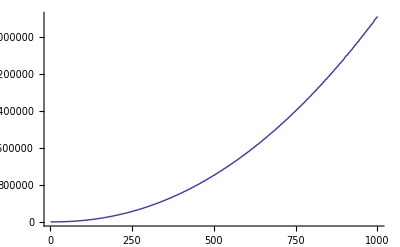

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
Reduce[x^3==x+1]
```

```mathematica
ToRadicals[{Root[-1-#1+#1^3&,1],Root[-1-#1+#1^3&,2],Root[-1-#1+#1^3&,3]}]
```

{1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3),-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3)),-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))}

```mathematica
DiscretePlot[(Root[-1-#1+#1^3&,1]^n+Root[-1-#1+#1^3&,2]^n+Root[-1-#1+#1^3&,3]^n),{n,1,10}]
```

```mathematica
∑_(n=0)^∞ ((1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3))^n+(1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3))^n+(1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3))^n)^-1
```

```mathematica
N[((9-√69)^(1/3)+(9+√69)^(1/3))/(3 (-2^(1/3) 3^(2/3)+(9-√69)^(1/3)+(9+√69)^(1/3)))]
```

1.35987

```mathematica
1/3((9-√69)^(1/3)/(-2^(1/3) 3^(2/3)+(9-√69)^(1/3)+(9+√69)^(1/3))+(9+√69)^(1/3)/(-2^(1/3) 3^(2/3)+(9-√69)^(1/3)+(9+√69)^(1/3)))
```

```mathematica
k==(9-√69)^(1/3)+(9+√69)^(1/3)
```

```mathematica
k/(k-18^(1/3))
```

```mathematica
Table[GCD[x,y],{x,1,1000},{y,1,1000}]//TableForm
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1
1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4
1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5
1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 3 | 2
1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8
1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1
1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 11 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 4
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 13 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2 | 7 | 2 | 1 | 2 | 1 | 2 | 1 | 14 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 3 | 5
1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 17 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2 | 1 | 6 | 1 | 2 | 3 | 2 | 1 | 18 | 1 | 2 | 3 | 2 | 1 | 6 | 1 | 2 | 9 | 2
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 20
1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1 | 7 | 3 | 1 | 1 | 3 | 1 | 1 | 21 | 1 | 1 | 3 | 1 | 1 | 3 | 7 | 1 | 3 | 1 | 1 | 3 | 1
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 11 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 22 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 23 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8
1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 1 | 1 | 25
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 13 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 26 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 9 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 27 | 1
1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4 | 7 | 2 | 1 | 4 | 1 | 2 | 1 | 28 | 1 | 2 | 1 | 4 | 1 | 2 | 7 | 4 | 1 | 2 | 1 | 4 | 1 | 14 | 1 | 4 | 1 | 2 | 1 | 4
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 29 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10 | 1 | 6 | 1 | 2 | 15 | 2 | 1 | 6 | 1 | 10 | 3 | 2 | 1 | 6 | 5 | 2 | 3 | 2 | 1 | 30 | 1 | 2 | 3 | 2 | 5 | 6 | 1 | 2 | 3 | 10
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 31 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 16 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 32 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 8
1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 11 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 11 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 33 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 17 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 34 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5 | 7 | 1 | 1 | 1 | 5 | 1 | 1 | 7 | 1 | 5 | 1 | 1 | 1 | 1 | 35 | 1 | 1 | 1 | 1 | 5 | 1 | 7 | 1 | 1 | 5 | 1 | 1 | 1 | 7 | 5 | 1 | 1 | 1 | 1 | 5
1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 36 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 4 | 9 | 2 | 1 | 12 | 1 | 2 | 3 | 4 | 1 | 18 | 1 | 4 | 3 | 2 | 1 | 12 | 1 | 2 | 9 | 4
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 37 | 1
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 19 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 38 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 13 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 39 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 13 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1
1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40 | 1 | 2 | 1 | 4 | 5 | 2 | 1 | 8 | 1 | 10 | 1 | 4 | 1 | 2 | 5 | 8 | 1 | 2 | 1 | 20 | 1 | 2 | 1 | 8 | 5 | 2 | 1 | 4 | 1 | 10 | 1 | 8 | 1 | 2 | 5 | 4 | 1 | 2 | 1 | 40
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 41 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2 | 7 | 6 | 1 | 2 | 3 | 2 | 1 | 42 | 1 | 2 | 3 | 2 | 1 | 6 | 7 | 2 | 3 | 2 | 1 | 6 | 1 | 14 | 3 | 2 | 1 | 6 | 1 | 2 | 21 | 2 | 1 | 6 | 1 | 2 | 3 | 14 | 1 | 6 | 1 | 2 | 3 | 2
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 43 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 11 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 44 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 11 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 22 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1 | 4
1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5 | 1 | 3 | 1 | 1 | 15 | 1 | 1 | 9 | 1 | 5 | 3 | 1 | 1 | 3 | 5 | 1 | 9 | 1 | 1 | 15 | 1 | 1 | 3 | 1 | 5 | 9 | 1 | 1 | 3 | 5 | 1 | 3 | 1 | 1 | 45 | 1 | 1 | 3 | 1 | 5 | 3 | 1 | 1 | 9 | 5
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 46 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 23 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 47 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 48 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 8 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 16 | 1 | 6 | 1 | 4 | 3 | 2 | 1 | 24 | 1 | 2 | 3 | 4 | 1 | 6 | 1 | 16 | 3 | 2 | 1 | 12 | 1 | 2 | 3 | 8
1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 49 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 25 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 50 | 1 | 2 | 1 | 2 | 5 | 2 | 1 | 2 | 1 | 10 | 1 | 2

```mathematica
GCD[a,b]==GCD[a±b,b]==GCD[Mod[a,b],b]
```

```mathematica
M[1,y]==M[x,1]==1
M[t,t]==t
M[x,y]==M[y,x]
M[x,y]==M[x+y,y]
```

```mathematica
Partition[Table[0,{x,1,100}],10]//MatrixForm
```

```mathematica
({{1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {1, 2, 1, 2, 1, 2, 1, 2, 1, 2}, {1, 1, 3, 1, 1, 3, 1, 1, 3, 1}, {1, 2, 1, 4, 1, 2, 1, 4, 1, 2}, {1, 1, 1, 1, 5, 1, 1, 1, 1, 5}, {1, 2, 3, 2, 1, 6, 1, 2, 3, 2}, {1, 1, 1, 1, 1, 1, 7, 1, 1, 1}, {1, 2, 1, 4, 1, 2, 1, 8, 1, 2}, {1, 1, 3, 1, 1, 3, 1, 1, 9, 1}, {1, 2, 1, 2, 5, 1, 1, 2, 1, 10}})
```

```mathematica
GCD[a,b]==GCD[a±b,b]==GCD[Mod[a,b],b]
M[x,y]==M[y,x]
M[0,t]==t
M[1,t]==1
M[t,t]==t
M[t+α,t]==M[Mod[α,t],t]
```

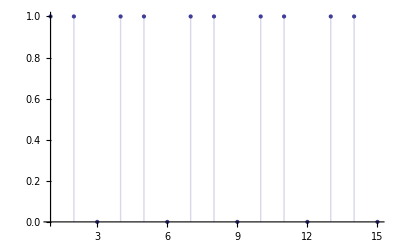

{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0}

```mathematica
b:=3
aa:=15
ff[x_]:=x^2
DiscretePlot[Mod[ff[x],b],{x,1,aa}]
Table[Mod[ff[x],b],{x,1,aa}]
```

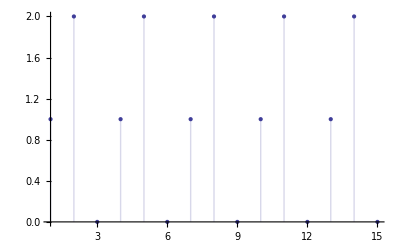

{1,2,0,1,2,0,1,2,0,1,2,0,1,2,0}

```mathematica
b:=3
aa:=15
ff[x_]:=x^3
DiscretePlot[Mod[ff[x],b],{x,1,aa}]
Table[Mod[ff[x],b],{x,1,aa}]
```

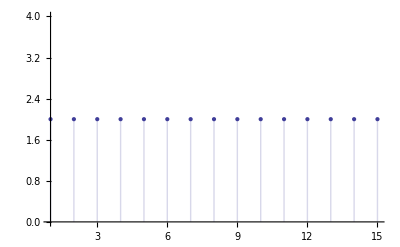

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
b:=3
aa:=15
ff[x_]:=x^3-x-1
DiscretePlot[Mod[ff[x],b],{x,1,aa}]
Table[Mod[ff[x],b],{x,1,aa}]
```

```mathematica
d[x_]:=(x-a)(x-c)
d[m*t+r]
Simplify[%]
Reduce[%==g+m*k&&k>0&&m>0&&g<m&&r<m&&r>0,Integers]
```

(-a+r+m t) (-c+r+m t)

(-a+r+m t) (-c+r+m t)

$Aborted

```mathematica
According to laws of congruences [ x'==Mod[x,m]⇒x'^i==Mod[x^i,m]]:
Mod[P[x],m]==Piecewise[{{Mod[P[1],m], Mod[x,m]==1}, {Mod[P[2],m], Mod[x,m]==2}, {., .}, {., .}, {., .}, {Mod[P[m-2],m], Mod[x,m]==(m-2)}, {Mod[P[m-1],m], Mod[x,m]==(m-1)}}]
```

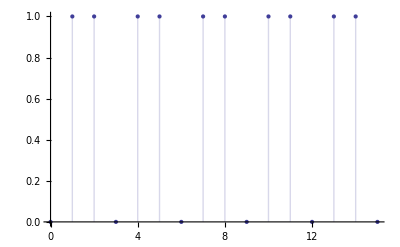

{0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0}

```mathematica
b:=3
aa:=15
ff[x_]:=x^2
DiscretePlot[Mod[ff[x],b],{x,0,aa}]
Table[Mod[ff[x],b],{x,0,aa}]
```

```mathematica
0->0
1->1
2->1
```

```mathematica
(3*x+0)^2==3*y+0
(3*x+1)^2==3*y+1
(3*x+2)^2==3*y+1
```

```mathematica
(3*x+0)^2/3==y
((3*x+1)^2-1)/3==y
((3*x+2)^2-1)/3==y
```

```mathematica
Table[{(3*x+0)^2/3,((3*x+1)^2-1)/3,((3*x+2)^2-1)/3},{x,0,10}]
```

{{0,0,1},{3,5,8},{12,16,21},{27,33,40},{48,56,65},{75,85,96},{108,120,133},{147,161,176},{192,208,225},{243,261,280},{300,320,341}}

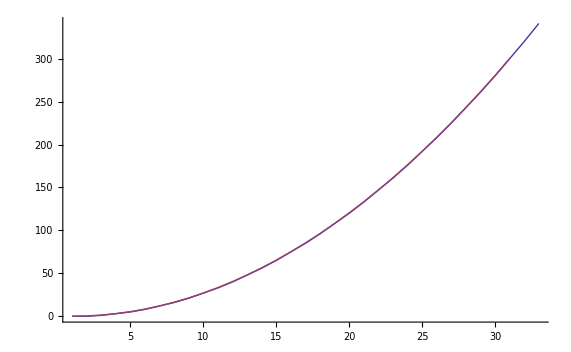

```mathematica
ListPlot[{Flatten[%],Table[x^2/3,{x,0,30}]},Joined->True]
```

```mathematica
¬(a∧b)⧦(¬a)∧(¬b)
```

!a&&!b⧦!(a&&b)

```mathematica
{{&&, and}, {||, or}, {!, not}, {el}, {fa}, {ex}, {!ex}, {xor}, {nand}, {nor}}
{{=>}, {}, {tf}, {}, {}, {}, {}, {}, {st}, {|}, {:}}
```

```mathematica
{"1"->"∧","2"->"∨","3"->"¬","4"->"∈","5"->"∀","6"->"∃","7"->"∄","8"->"⊻","9"->"⊼","0"->"⊽","A"->"⇒","B"->"∴","C"->"∍","D"->"|","E"->"∶","F"->""}
```

```mathematica
Table[StringReplace[ToString[x],{"{"->"","}"->"","1,"->"∧","2,"->"∨","3,"->"¬","4,"->"∈","5,"->"∀","6,"->"∃","7,"->"∄","8,"->"⊻","9,"->"⊼","0,"->"⊽","10,"->"⇒","11,"->"∴","12,"->"∍","13,"->"|","14,"->"∶","15,"->"","16,"->"x_1","17,"->"x_2","18,"->"x_3"}],{x,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
a∧b∈Integers⇒(a+b)∈Integers
```

a&&b∈Integers⇒a+b∈Integers

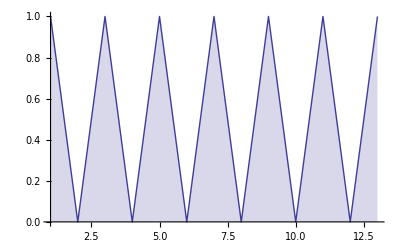
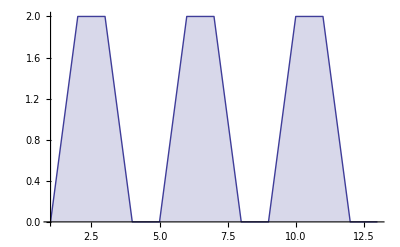
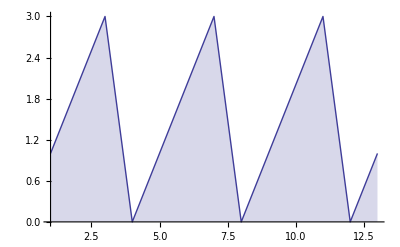
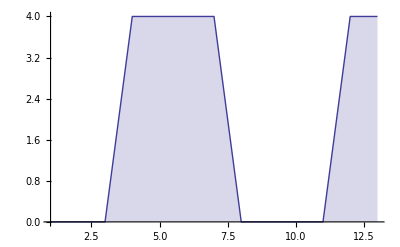
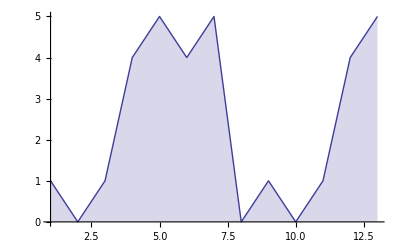
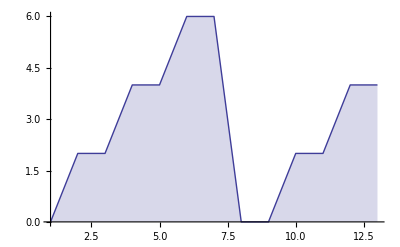
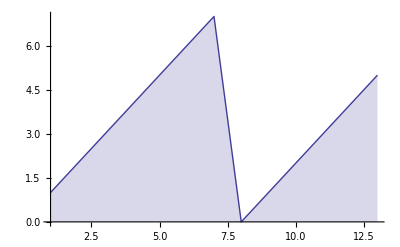
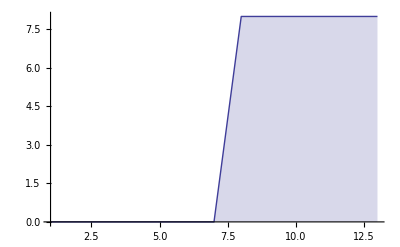

```mathematica
aa:=13
Table[DiscretePlot[BitAnd[x,y],{x,1,aa},Joined->True],{y,1,aa}]
```

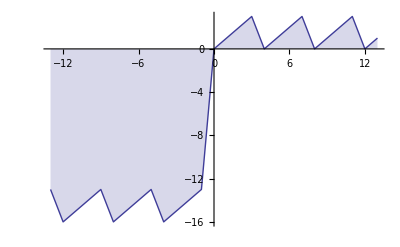
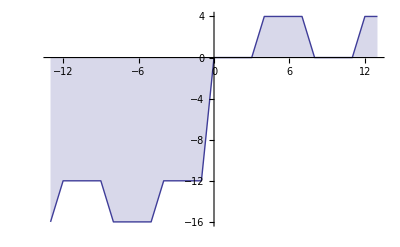
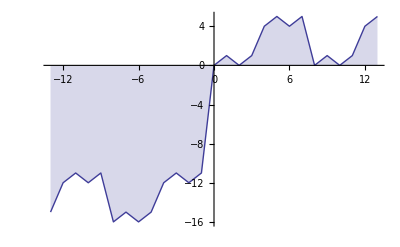
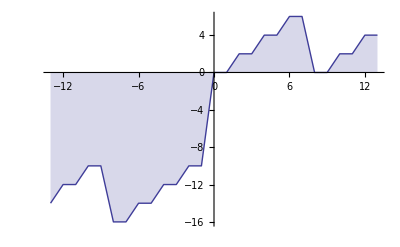
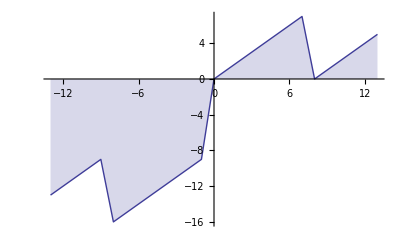
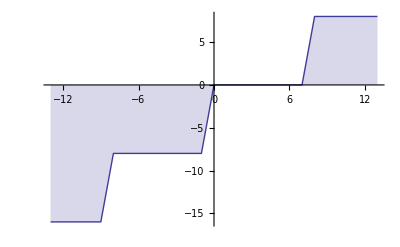
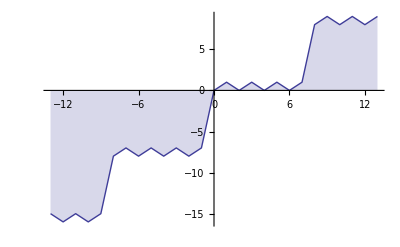
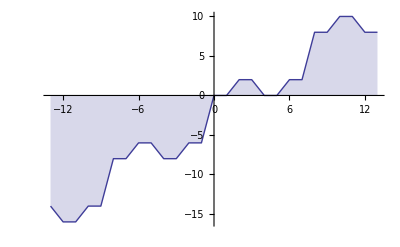

```mathematica
aa:=13
Table[DiscretePlot[BitAnd[x,y],{x,-aa,aa},Joined->True],{y,-aa,aa}]
```

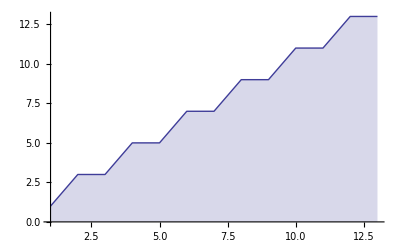
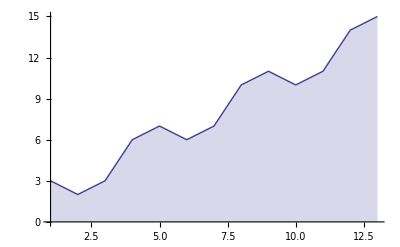
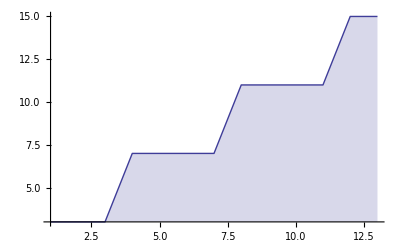
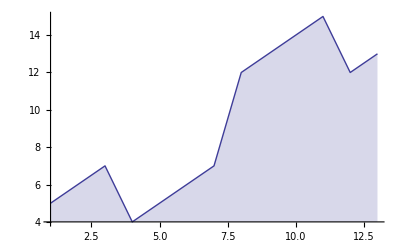
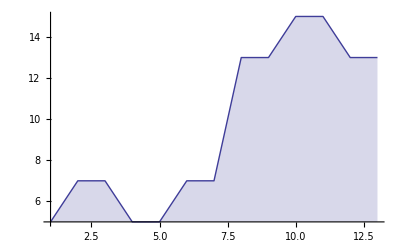
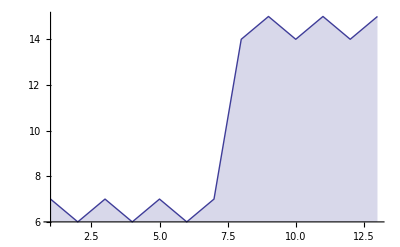
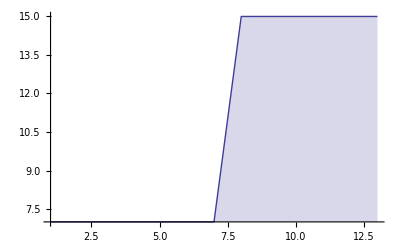
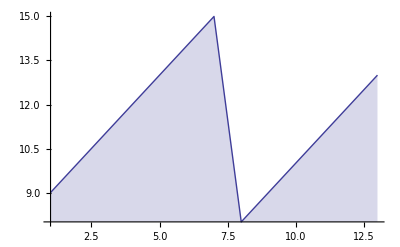

```mathematica
aa:=13
Table[DiscretePlot[BitOr[x,y],{x,1,aa},Joined->True],{y,1,aa}]
```

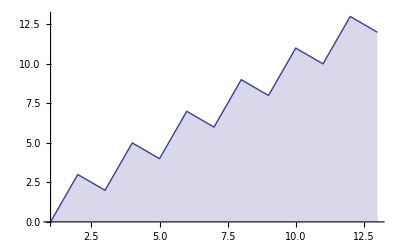
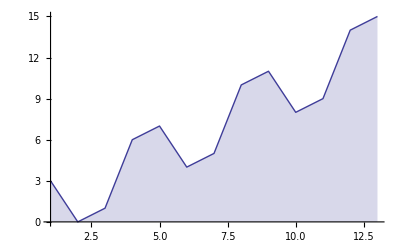
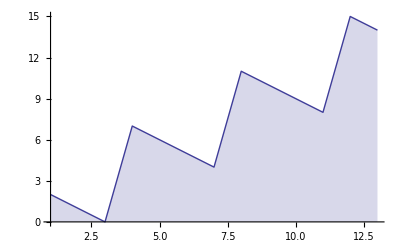
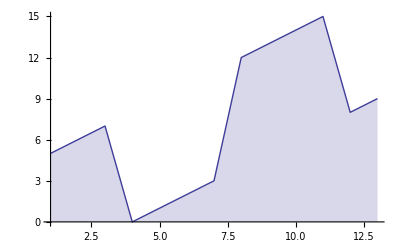
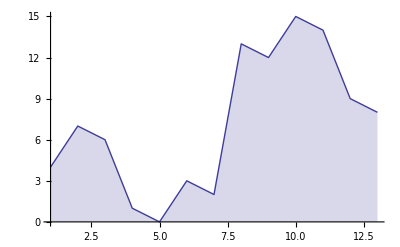
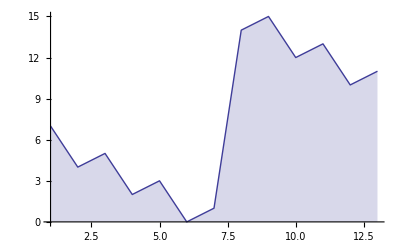
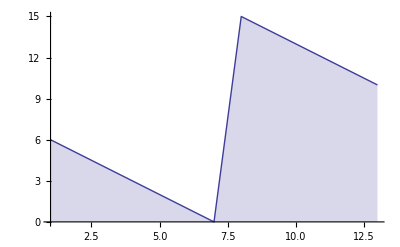
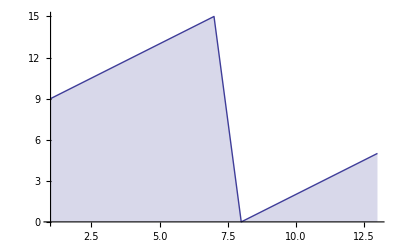

```mathematica
aa:=13
Table[DiscretePlot[BitXor[x,y],{x,1,aa},Joined->True],{y,1,aa}]
```

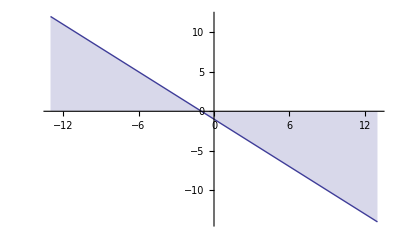

```mathematica
aa:=13
DiscretePlot[BitNot[x],{x,-aa,aa},Joined->True]
```

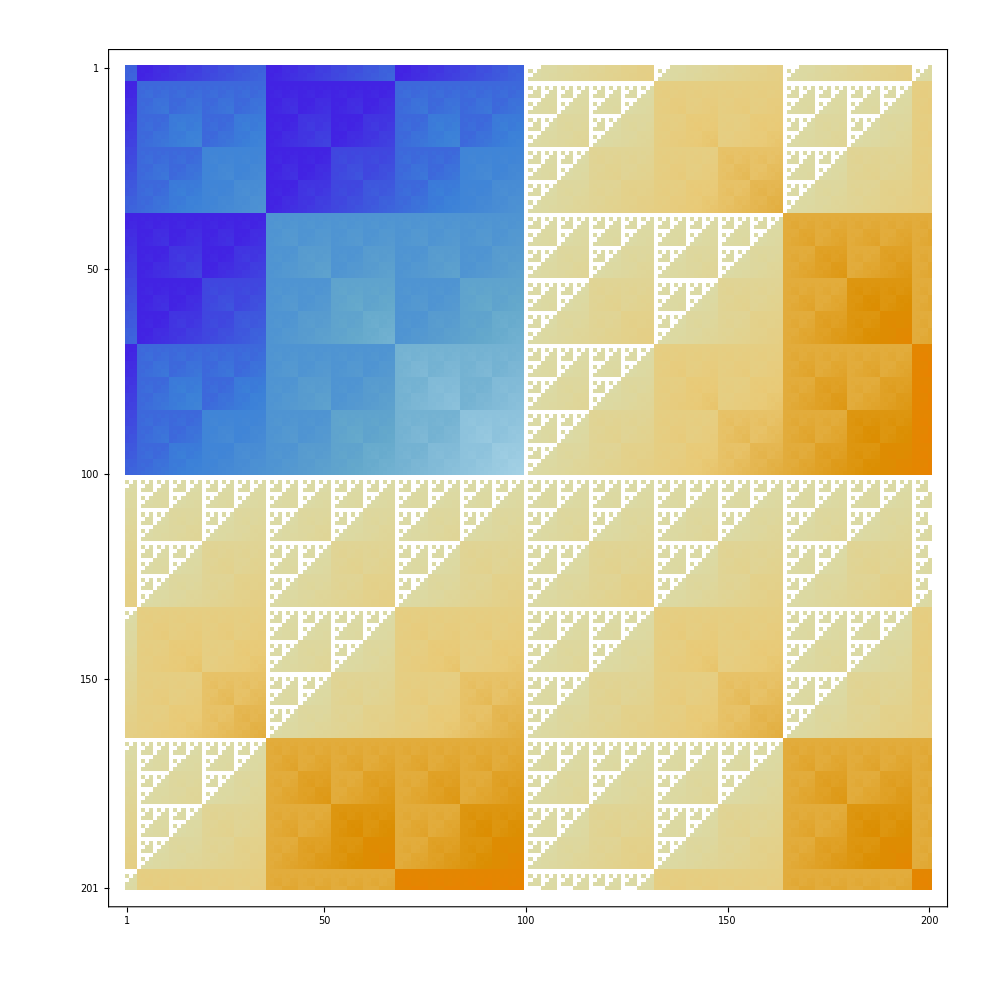

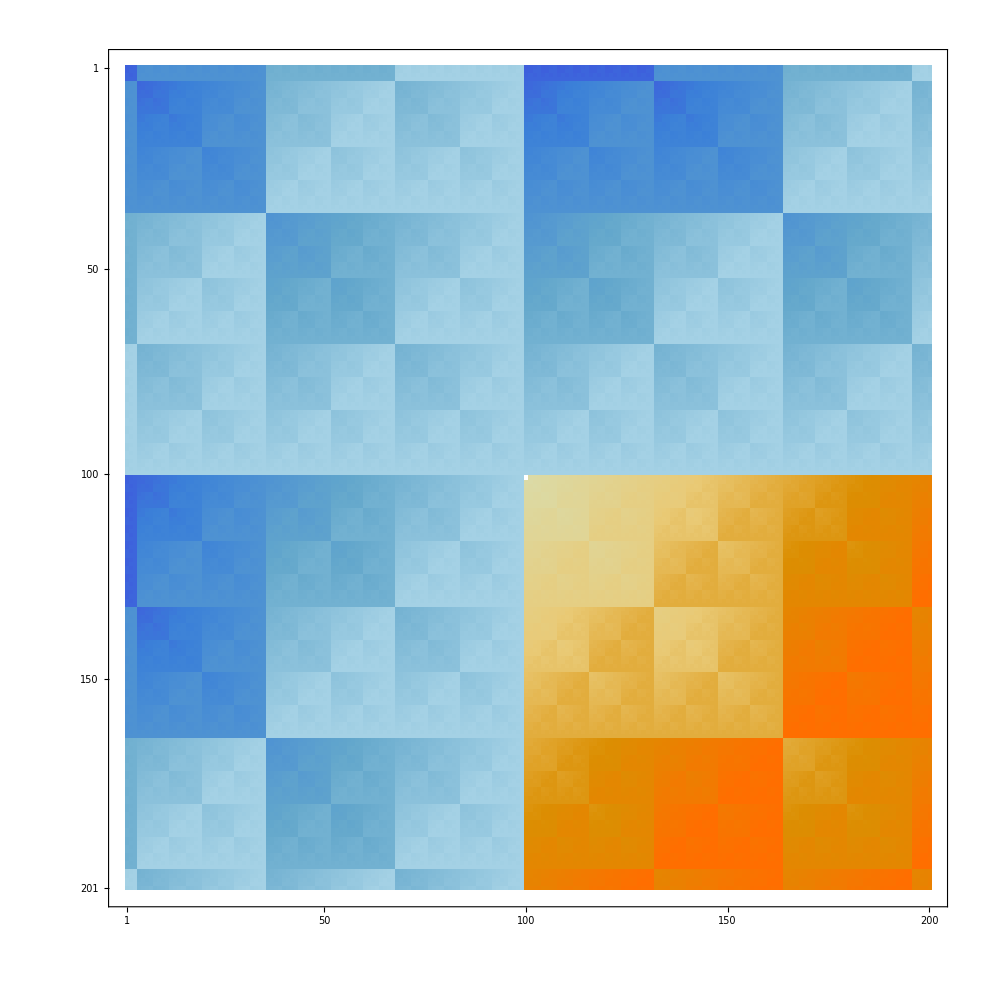

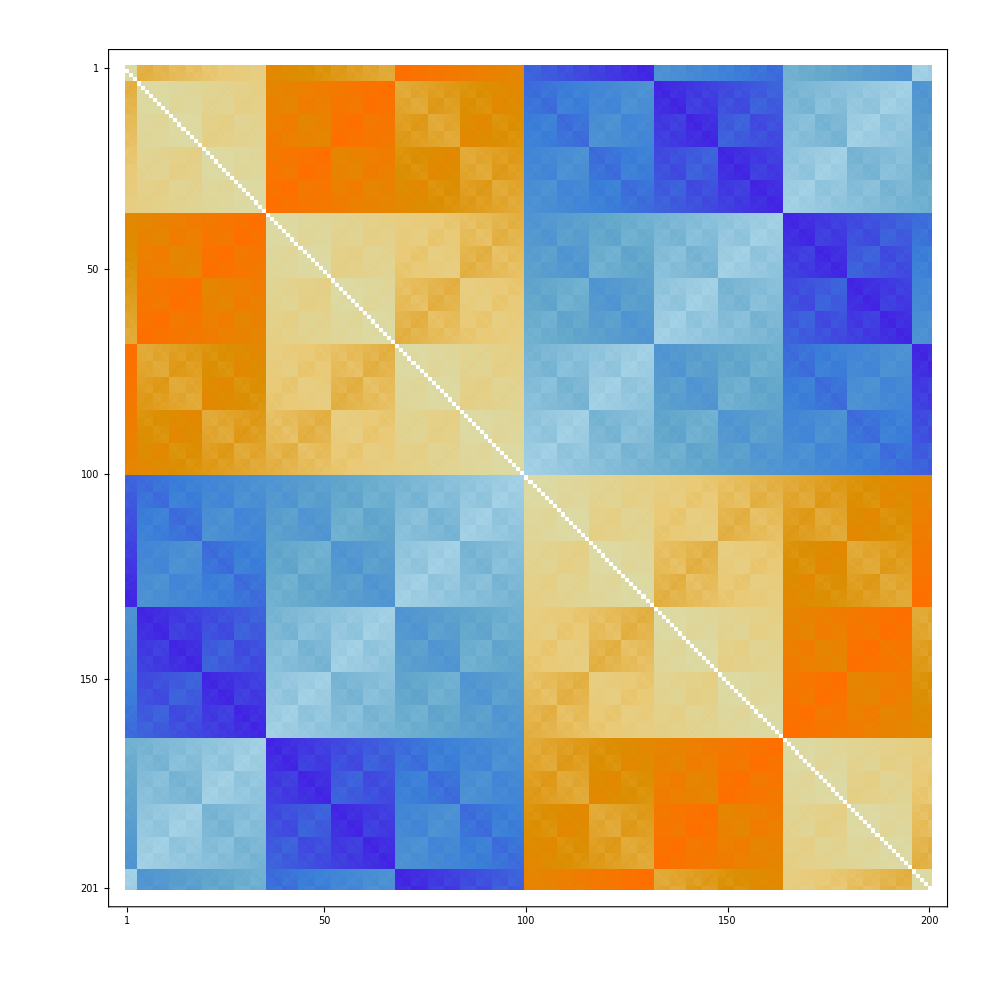

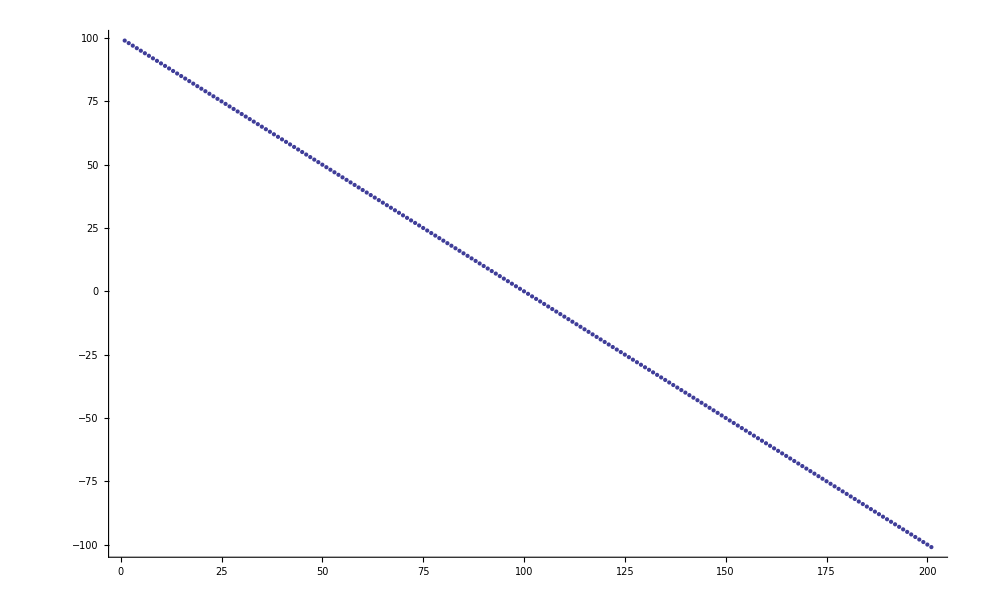

```mathematica
aa:=100
MatrixPlot[Table[BitAnd[x,y],{x,-aa,aa},{y,1-aa,aa}]]
MatrixPlot[Table[BitOr[x,y],{x,-aa,aa},{y,1-aa,aa}]]
MatrixPlot[Table[BitXor[x,y],{x,-aa,aa},{y,1-aa,aa}]]
ListPlot[Table[BitNot[x],{x,-aa,aa}]]
```

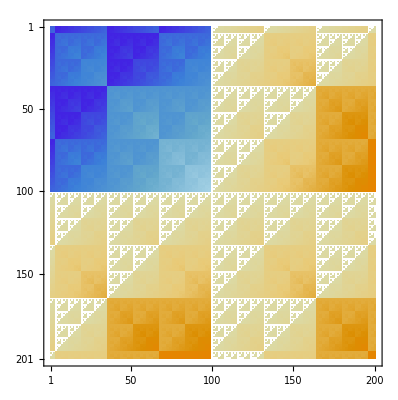
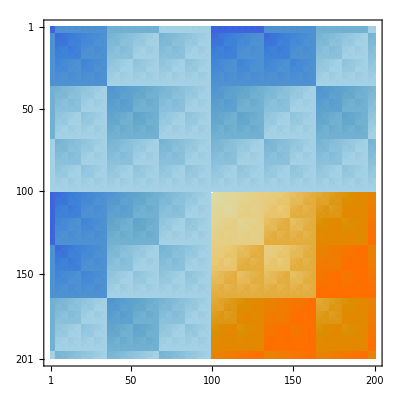
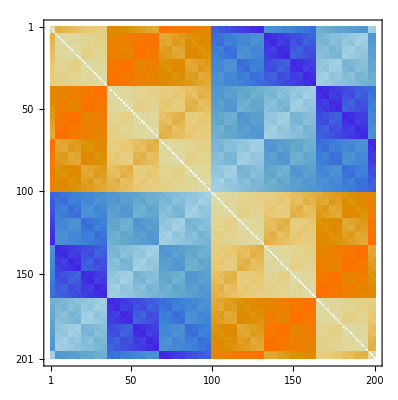
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa:=100
{MatrixPlot[Table[BitAnd[BitAnd[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitAnd[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitAnd[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitOr[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitOr[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitOr[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitXor[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitXor[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitAnd[BitXor[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitAnd[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitAnd[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitAnd[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitOr[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitOr[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitOr[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitXor[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitXor[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitOr[BitXor[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitAnd[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitAnd[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitAnd[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitOr[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitOr[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitOr[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitXor[x,y],BitAnd[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitXor[x,y],BitOr[x,y]],{x,-aa,aa},{y,1-aa,aa}]],MatrixPlot[Table[BitXor[BitXor[x,y],BitXor[x,y]],{x,-aa,aa},{y,1-aa,aa}]]}
```

```mathematica
6,1
5,2
10,3
6,4
```

```mathematica
Map[MatrixForm,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,16}]],2],2]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1),(0 | 0
0 | 0)}

```mathematica
s[x_,y_,({{a_, b_}, {c_, d_}})]:=Piecewise[{{c, x==0&&y==0}, {a, x==0&&y==1}, {b, x==1&&y==0}, {d, x==1&&y==1}}]
```

```mathematica
Map[Nor,{{-1,1},{1,-1}}]
```

{!{-1,1},!{1,-1}}

```mathematica
Part[IntegerDigits[y,2],i]
```

```mathematica
s[{x_,y_,i_,({{a_, b_}, {c_, d_}})}]:=Piecewise[{{c, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0}, {a, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1}, {b, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0}, {d, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1}}]

t[x_,y_,({{a_, b_}, {c_, d_}})]:=FromDigits[Table[s[{x,y,i,({{a, b}, {c, d}})}],{i,1,Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]}],2]
```

```mathematica
M[m_]:=MatrixPlot[Table[t[x,y,m],{x,-aa,aa},{y,-aa,aa}]]
```

```mathematica
aa:=100
Map[MatrixForm,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,2^4-1}]],2],2]]
Map[M,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,2^4-1}]],2],2]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
l:=Piecewise[{{Length[IntegerDigits[x,2], x>y}, {Length[IntegerDigits[y,2], x<y}, {Length[IntegerDigits[x,2], x==y}}]
```

```mathematica
FromDigits[{1,1,0,1,1,1,0,1},2]
```

221

```mathematica
PadLeft[{1,1},4]
```

{0,0,1,1}

```mathematica
Part[{1,2,3,4,5},1]
```

1

```mathematica
Table[ToString[{a,b}],{a,1,5},{b,1,5}]//MatrixForm
```

({1, 1} | {1, 2} | {1, 3} | {1, 4} | {1, 5}
{2, 1} | {2, 2} | {2, 3} | {2, 4} | {2, 5}
{3, 1} | {3, 2} | {3, 3} | {3, 4} | {3, 5}
{4, 1} | {4, 2} | {4, 3} | {4, 4} | {4, 5}
{5, 1} | {5, 2} | {5, 3} | {5, 4} | {5, 5})

```mathematica
pos[2,3]==12
pos[3,2]==8
pos[a,b]==B*b+a-1
pos[2,3]==5*2+3-1==12
```

```mathematica
B:=3
h[B_]:=Partition[Table[Subscript[x, i],{i,1,B^2}],B]
tk[x_,y_,i_,B_]:=Part[PadLeft[IntegerDigits[x,B],Piecewise[{{Length[IntegerDigits[x,B]], x>y}, {Length[IntegerDigits[y,B]], x<y}, {Length[IntegerDigits[x,B]], x==y}}]],i]
S[{x_,y_,i_,({{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3]}, {Subscript[x, 4], Subscript[x, 5], Subscript[x, 6]}, {Subscript[x, 7], Subscript[x, 8], Subscript[x, 9]}}),B_}]:=Piecewise[Table[{Subscript[x, (B*j+k-1)],tk[x,y,i,B]==j&&tk[y,x,i,B]==k},{j,1,B},{k,1,B}]]
T[{x_,y_,({{Subscript[x, 1]_, Subscript[x, 2]_}, {Subscript[x, 3]_, Subscript[x, 4]_}}),B_}]:=FromDigits[Table[S[{x,y,i,h[B],B}],{i,1,Piecewise[{{Length[IntegerDigits[x,B]], x>y}, {Length[IntegerDigits[y,B]], x<y}, {Length[IntegerDigits[x,B]], x==y}}]}],B]
```

```mathematica
h[B]//MatrixForm
```

(x_1 | x_2 | x_3
x_4 | x_5 | x_6
x_7 | x_8 | x_9)

```mathematica
({{Subscript[x, 1], Subscript[x, 2]}, {Subscript[x, 3], Subscript[x, 4]}})
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

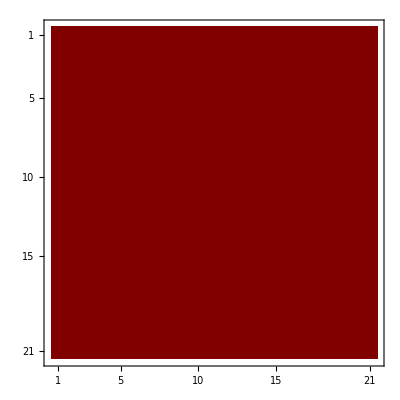
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(x_1 | x_2 | x_3
x_4 | x_5 | x_6
x_7 | x_8 | x_9)

```mathematica
aa:=10
M[m_]:=MatrixPlot[Table[t[x,y,m,B],{x,-aa,aa},{y,-aa,aa}]]
Map[MatrixForm,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,B],2B],{x,0,B^(B^2)-1}]],B],B]]
Map[M,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,B],2B],{x,0,B^(B^2)-1}]],B],B]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

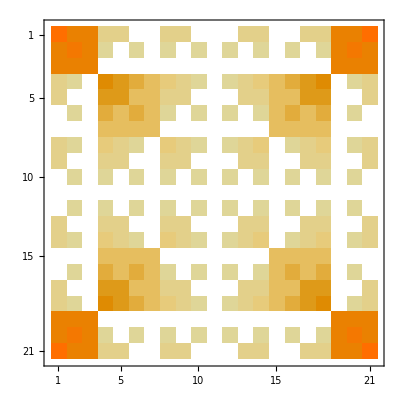
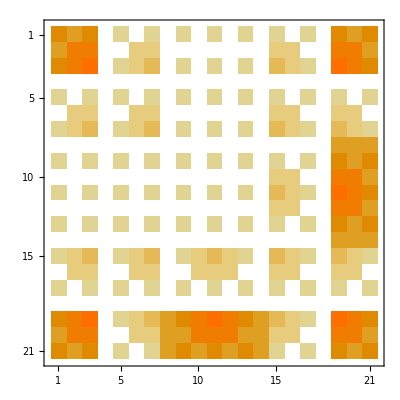
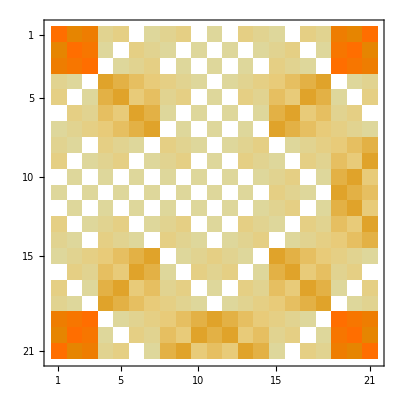
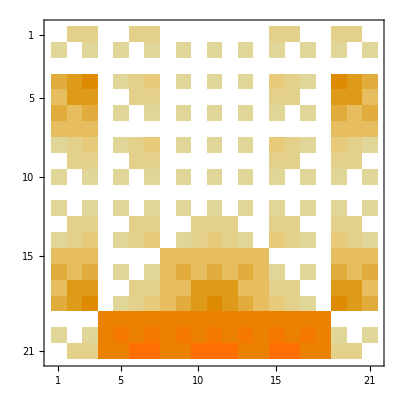
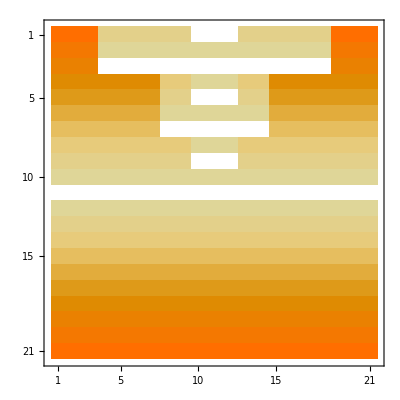
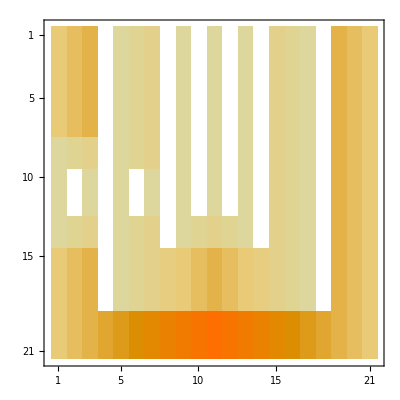
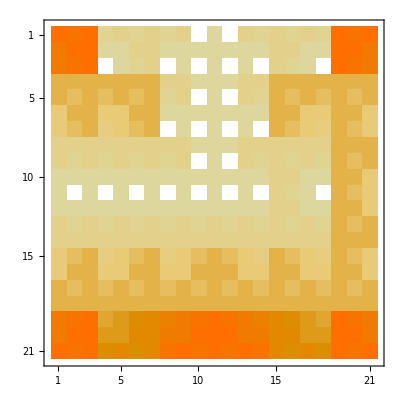
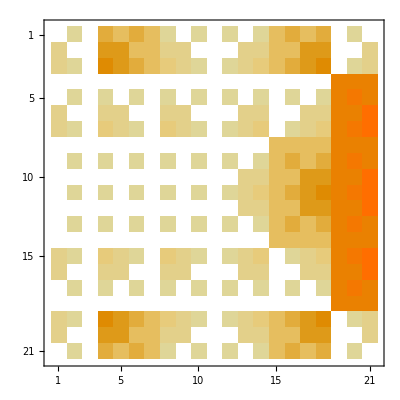
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
s[{x_,y_,i_,({{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3]}, {Subscript[x, 4], Subscript[x, 5], Subscript[x, 6]}, {Subscript[x, 7], Subscript[x, 8], Subscript[x, 9]}})}]:=Piecewise[{{c, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0}, {a, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1}, {b, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0}, {d, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1}}]

t[x_,y_,({{a_, b_}, {c_, d_}})]:=FromDigits[Table[s[{x,y,i,({{a, b}, {c, d}})}],{i,1,Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]}],2]
M[m_]:=MatrixPlot[Table[t[x,y,m],{x,-aa,aa},{y,-aa,aa}]]
aa:=10
Map[MatrixForm,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,2^4-1}]],2],2]]
Map[M,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,2^4-1}]],2],2]]
```

```mathematica
1.1
2.1
3.1
4.1
5.2
6.2
7.2
8.2
13.1
14.1
15.1
16.1
```

```mathematica
B:=3
h[B_]:=Partition[Table[Subscript[x, i],{i,1,B^2}],B]
tk[x_,y_,i_,B_]:=Part[PadLeft[IntegerDigits[x,B],Piecewise[{{Length[IntegerDigits[x,B]], x>y}, {Length[IntegerDigits[y,B]], x<y}, {Length[IntegerDigits[x,B]], x==y}}]],i]
ss[{x_,y_,i_,({{x1_, x2_, x3_}, {x4_, x5_, x6_}, {x7_, x8_, x9_}}),B_}]:=Piecewise[Table[{ToExpression[StringJoin["x",ToString[(B*j+k-1)]]],tk[x,y,i,B]==j&&tk[y,x,i,B]==k},{j,1,B},{k,1,B}]]
tt[{x_,y_,({{x1_, x2_, x3_}, {x4_, x5_, x6_}, {x7_, x8_, x9_}}),B_}]:=FromDigits[Table[S[{x,y,i,h[B],B}],{i,1,Piecewise[{{Length[IntegerDigits[x,B]], x>y}, {Length[IntegerDigits[y,B]], x<y}, {Length[IntegerDigits[x,B]], x==y}}]}],B]
```

```mathematica
aa:=10
M[m_]:=MatrixPlot[Table[tt[x,y,m,B],{x,-aa,aa},{y,-aa,aa}]]
Map[MatrixForm,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,B],2B],{x,0,B^(B^2)-1}]],B],B]]
Map[M,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,B],2B],{x,0,B^(B^2)-1}]],B],B]]
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 2),(0 | 0 | 0
0 | 1 | 0
0 | 0 | 0),(0 | 1 | 1
0 | 0 | 0
0 | 1 | 2),(0 | 0 | 0
0 | 2 | 0
0 | 0 | 0),(0 | 2 | 1
0 | 0 | 0
0 | 2 | 2),(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0),(1 | 0 | 1
0 | 0 | 0
1 | 0 | 2),(0 | 0 | 0
1 | 1 | 0
0 | 0 | 0),(1 | 1 | 1
0 | 0 | 0
1 | 1 | 2),(0 | 0 | 0
1 | 2 | 0
0 | 0 | 0),(1 | 2 | 1
0 | 0 | 0
1 | 2 | 2),(0 | 0 | 0
2 | 0 | 0
0 | 0 | 0),(2 | 0 | 1
0 | 0 | 0
2 | 0 | 2),(0 | 0 | 0
2 | 1 | 0
0 | 0 | 0),(2 | 1 | 1
0 | 0 | 0
2 | 1 | 2),(0 | 0 | 0
2 | 2 | 0
0 | 0 | 0),(2 | 2 | 1
0 | 0 | 0
2 | 2 | 2),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 1),(0 | 0 | 1
0 | 0 | 1
0 | 0 | 2),(0 | 0 | 1
0 | 1 | 0
0 | 0 | 1),(0 | 1 | 1
0 | 0 | 1
0 | 1 | 2),(0 | 0 | 1
0 | 2 | 0
0 | 0 | 1),(0 | 2 | 1
0 | 0 | 1
0 | 2 | 2),(0 | 0 | 1
1 | 0 | 0
0 | 0 | 1),(1 | 0 | 1
0 | 0 | 1
1 | 0 | 2),(0 | 0 | 1
1 | 1 | 0
0 | 0 | 1),(1 | 1 | 1
0 | 0 | 1
1 | 1 | 2),(0 | 0 | 1
1 | 2 | 0
0 | 0 | 1),(1 | 2 | 1
0 | 0 | 1
1 | 2 | 2),(0 | 0 | 1
2 | 0 | 0
0 | 0 | 1),(2 | 0 | 1
0 | 0 | 1
2 | 0 | 2),(0 | 0 | 1
2 | 1 | 0
0 | 0 | 1),(2 | 1 | 1
0 | 0 | 1
2 | 1 | 2),(0 | 0 | 1
2 | 2 | 0
0 | 0 | 1),(2 | 2 | 1
0 | 0 | 1
2 | 2 | 2),(0 | 0 | 2
0 | 0 | 0
0 | 0 | 2),(0 | 0 | 1
0 | 0 | 2
0 | 0 | 2),(0 | 0 | 2
0 | 1 | 0
0 | 0 | 2),(0 | 1 | 1
0 | 0 | 2
0 | 1 | 2),(0 | 0 | 2
0 | 2 | 0
0 | 0 | 2),(0 | 2 | 1
0 | 0 | 2
0 | 2 | 2),(0 | 0 | 2
1 | 0 | 0
0 | 0 | 2),(1 | 0 | 1
0 | 0 | 2
1 | 0 | 2),(0 | 0 | 2
1 | 1 | 0
0 | 0 | 2),(1 | 1 | 1
0 | 0 | 2
1 | 1 | 2),(0 | 0 | 2
1 | 2 | 0
0 | 0 | 2),(1 | 2 | 1
0 | 0 | 2
1 | 2 | 2),(0 | 0 | 2
2 | 0 | 0
0 | 0 | 2),(2 | 0 | 1
0 | 0 | 2
2 | 0 | 2),(0 | 0 | 2
2 | 1 | 0
0 | 0 | 2),(2 | 1 | 1
0 | 0 | 2
2 | 1 | 2),(0 | 0 | 2
2 | 2 | 0
0 | 0 | 2),(2 | 2 | 1
0 | 0 | 2
2 | 2 | 2),(0 | 1 | 0
0 | 0 | 0
0 | 1 | 0),(0 | 0 | 1
0 | 1 | 0
0 | 0 | 2),(0 | 1 | 0
0 | 1 | 0
0 | 1 | 0),(0 | 1 | 1
0 | 1 | 0
0 | 1 | 2),(0 | 1 | 0
0 | 2 | 0
0 | 1 | 0),(0 | 2 | 1
0 | 1 | 0
0 | 2 | 2),(0 | 1 | 0
1 | 0 | 0
0 | 1 | 0),(1 | 0 | 1
0 | 1 | 0
1 | 0 | 2),(0 | 1 | 0
1 | 1 | 0
0 | 1 | 0),(1 | 1 | 1
0 | 1 | 0
1 | 1 | 2),(0 | 1 | 0
1 | 2 | 0
0 | 1 | 0),(1 | 2 | 1
0 | 1 | 0
1 | 2 | 2),«12990»,(2 | 1 | 2
1 | 0 | 0
2 | 1 | 2),(1 | 0 | 1
2 | 1 | 2
1 | 0 | 2),(2 | 1 | 2
1 | 1 | 0
2 | 1 | 2),(1 | 1 | 1
2 | 1 | 2
1 | 1 | 2),(2 | 1 | 2
1 | 2 | 0
2 | 1 | 2),(1 | 2 | 1
2 | 1 | 2
1 | 2 | 2),(2 | 1 | 2
2 | 0 | 0
2 | 1 | 2),(2 | 0 | 1
2 | 1 | 2
2 | 0 | 2),(2 | 1 | 2
2 | 1 | 0
2 | 1 | 2),(2 | 1 | 1
2 | 1 | 2
2 | 1 | 2),(2 | 1 | 2
2 | 2 | 0
2 | 1 | 2),(2 | 2 | 1
2 | 1 | 2
2 | 2 | 2),(2 | 2 | 0
0 | 0 | 0
2 | 2 | 0),(0 | 0 | 1
2 | 2 | 0
0 | 0 | 2),(2 | 2 | 0
0 | 1 | 0
2 | 2 | 0),(0 | 1 | 1
2 | 2 | 0
0 | 1 | 2),(2 | 2 | 0
0 | 2 | 0
2 | 2 | 0),(0 | 2 | 1
2 | 2 | 0
0 | 2 | 2),(2 | 2 | 0
1 | 0 | 0
2 | 2 | 0),(1 | 0 | 1
2 | 2 | 0
1 | 0 | 2),(2 | 2 | 0
1 | 1 | 0
2 | 2 | 0),(1 | 1 | 1
2 | 2 | 0
1 | 1 | 2),(2 | 2 | 0
1 | 2 | 0
2 | 2 | 0),(1 | 2 | 1
2 | 2 | 0
1 | 2 | 2),(2 | 2 | 0
2 | 0 | 0
2 | 2 | 0),(2 | 0 | 1
2 | 2 | 0
2 | 0 | 2),(2 | 2 | 0
2 | 1 | 0
2 | 2 | 0),(2 | 1 | 1
2 | 2 | 0
2 | 1 | 2),(2 | 2 | 0
2 | 2 | 0
2 | 2 | 0),(2 | 2 | 1
2 | 2 | 0
2 | 2 | 2),(2 | 2 | 1
0 | 0 | 0
2 | 2 | 1),(0 | 0 | 1
2 | 2 | 1
0 | 0 | 2),(2 | 2 | 1
0 | 1 | 0
2 | 2 | 1),(0 | 1 | 1
2 | 2 | 1
0 | 1 | 2),(2 | 2 | 1
0 | 2 | 0
2 | 2 | 1),(0 | 2 | 1
2 | 2 | 1
0 | 2 | 2),(2 | 2 | 1
1 | 0 | 0
2 | 2 | 1),(1 | 0 | 1
2 | 2 | 1
1 | 0 | 2),(2 | 2 | 1
1 | 1 | 0
2 | 2 | 1),(1 | 1 | 1
2 | 2 | 1
1 | 1 | 2),(2 | 2 | 1
1 | 2 | 0
2 | 2 | 1),(1 | 2 | 1
2 | 2 | 1
1 | 2 | 2),(2 | 2 | 1
2 | 0 | 0
2 | 2 | 1),(2 | 0 | 1
2 | 2 | 1
2 | 0 | 2),(2 | 2 | 1
2 | 1 | 0
2 | 2 | 1),(2 | 1 | 1
2 | 2 | 1
2 | 1 | 2),(2 | 2 | 1
2 | 2 | 0
2 | 2 | 1),(2 | 2 | 1
2 | 2 | 1
2 | 2 | 2),(2 | 2 | 2
0 | 0 | 0
2 | 2 | 2),(0 | 0 | 1
2 | 2 | 2
0 | 0 | 2),(2 | 2 | 2
0 | 1 | 0
2 | 2 | 2),(0 | 1 | 1
2 | 2 | 2
0 | 1 | 2),(2 | 2 | 2
0 | 2 | 0
2 | 2 | 2),(0 | 2 | 1
2 | 2 | 2
0 | 2 | 2),(2 | 2 | 2
1 | 0 | 0
2 | 2 | 2),(1 | 0 | 1
2 | 2 | 2
1 | 0 | 2),(2 | 2 | 2
1 | 1 | 0
2 | 2 | 2),(1 | 1 | 1
2 | 2 | 2
1 | 1 | 2),(2 | 2 | 2
1 | 2 | 0
2 | 2 | 2),(1 | 2 | 1
2 | 2 | 2
1 | 2 | 2),(2 | 2 | 2
2 | 0 | 0
2 | 2 | 2),(2 | 0 | 1
2 | 2 | 2
2 | 0 | 2),(2 | 2 | 2
2 | 1 | 0
2 | 2 | 2),(2 | 1 | 1
2 | 2 | 2
2 | 1 | 2),(2 | 2 | 2
2 | 2 | 0
2 | 2 | 2),(2 | 2 | 1
2 | 2 | 2
2 | 2 | 2)}

$Aborted

```mathematica
s[{x_,y_,i_,({{a_, b_}, {c_, d_}})}]:=Piecewise[{{c, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0}, {a, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1}, {b, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==0}, {d, Part[PadLeft[IntegerDigits[x,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1&&Part[PadLeft[IntegerDigits[y,2],Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]],i]==1}}]

t[x_,y_,({{a_, b_}, {c_, d_}})]:=FromDigits[Table[s[{x,y,i,({{a, b}, {c, d}})}],{i,1,Piecewise[{{Length[IntegerDigits[x,2]], x>y}, {Length[IntegerDigits[y,2]], x<y}, {Length[IntegerDigits[x,2]], x==y}}]}],2]
M[m_]:=MatrixPlot[Table[t[x,y,m],{x,-aa,aa},{y,-aa,aa}]]
aa:=5
Map[MatrixForm,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,2^4-1}]],2],2]]
Map[M,Partition[Partition[Flatten[Table[PadLeft[IntegerDigits[x,2],4],{x,0,2^4-1}]],2],2]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
c[({{a_, b_}, {c_, d_}}),({{e_, f_}, {g_, h_}}),({{i_, j_}, {k_, l_}})]:={({{a, b}, {c, d}}),({{e, f}, {g, h}}),({{i, j}, {k, l}}),({{t[a,e,({{i, j}, {k, l}})], t[b,f,({{i, j}, {k, l}})]}, {t[c,g,({{i, j}, {k, l}})], t[d,h,({{i, j}, {k, l}})]}})}
```

```mathematica
Partition[Partition[Partition[Flatten[Table[c[Partition[Flatten[PadLeft[IntegerDigits[x,2],4]],2],Partition[Flatten[PadLeft[IntegerDigits[y,2],4]],2],Partition[Flatten[PadLeft[IntegerDigits[z,2],4]],2]],{x,0,15},{y,0,15},{z,0,15}]],2],2],4]//MatrixForm
```

((0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0)
(0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0)
(0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 1) | (1 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 0
1 | 1) | (1 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 0) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
0 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1) | (1 | 1
1 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 0) | (0 | 1
0 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 0) | (0 | 0
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 0) | (0 | 1
0 | 0)
(1 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 0) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 0) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 0) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
0 | 1) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 0
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (1 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (0 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0) | (1 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 1) | (1 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
0 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 0) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 0) | (1 | 0
1 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 0
1 | 1) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 0) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 0) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (0 | 1
1 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 1) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
0 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 0) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 0
1 | 1) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (0 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 0) | (0 | 0
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
1 | 1) | (1 | 0
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 0) | (0 | 1
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
0 | 1) | (1 | 0
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 0
1 | 1) | (1 | 0
1 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 1
0 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (0 | 1
1 | 1) | (1 | 1
1 | 0)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)
(1 | 1
0 | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (

```mathematica
rr[({{1, 1}, {0, 0}})]
```

{{1, 1}, {0, 0}}

```mathematica
Clear[x,y,z]
```

```mathematica
({{1, 1}, {0, 0}})
```